## Jaki’s Plot Styles

```mathematica
Needs["ErrorBarPlots`"]
thick=0.008;
MyStyle={Directive[Thickness[thick],Black],
Directive[Thickness[thick],Dashing[{0.03,0.03}],Darker[Red]],
Directive[Thickness[thick],Dashing[{0.015,0.02,0.001,0.02}],Blue],
Directive[Thickness[thick],Dashing[{0.005,0.02}],Brown],
Directive[Thickness[thick],Dashing[{0.005,0.02}],Green],
Directive[Thickness[thick],Dashing[{0.03,0.03}],Lighter[Red]],
Directive[Thickness[thick],Dashing[{0.015,0.02,0.001,0.02}],Darker[Brown]],
Directive[Thickness[thick],Darker[Orange]],
Directive[Thickness[thick],Darker[Purple]],
Directive[Thickness[thick],Darker[Magenta]],
Directive[Thickness[thick],Blue],
Directive[Thickness[thick],Red],
Directive[Thickness[thick],Green],
Directive[Thickness[thick],Brown],
Directive[Thickness[thick],Orange],
Directive[Thickness[thick],Purple],
Directive[Thickness[thick],Magenta],
Directive[Thickness[thick],Dashing[{0.005,0.02}],Darker[Blue]],
Directive[Thickness[thick],Dashing[{0.03,0.03}],Darker[Yellow]]};
MyStyle2={Directive[Thickness[thick],Black],
Directive[Thickness[thick],Blue],
Directive[Thickness[thick],Dashing[{0.005,0.02}],Blue],
Directive[Thickness[thick],Darker[Red]],
Directive[Thickness[thick],Dashing[{0.015,0.02,0.001,0.02}],Darker[Red]],
Directive[Thickness[thick],Darker[Green]],
Directive[Thickness[thick],Dashing[{0.015,0.02,0.001,0.02}],Darker[Green]],
Directive[Thickness[thick],Darker[Yellow]],
Directive[Thickness[thick],Dashing[{0.03,0.03}],Darker[Yellow]],
Directive[Thickness[thick],Dashing[{0.015,0.02,0.001,0.02}],Darker[Brown]],
Directive[Thickness[thick],Darker[Orange]],
Directive[Thickness[thick],Darker[Purple]],
Directive[Thickness[thick],Darker[Magenta]],
Directive[Thickness[thick],Blue],
Directive[Thickness[thick],Red],
Directive[Thickness[thick],Green],
Directive[Thickness[thick],Brown],
Directive[Thickness[thick],Orange],
Directive[Thickness[thick],Purple],
Directive[Thickness[thick],Magenta],
Directive[Thickness[thick],Dashing[{0.005,0.02}],Darker[Blue]],
Directive[Thickness[thick],Dashing[{0.03,0.03}],Darker[Yellow]]};
MyStyle3={Directive[Thickness[thick],Black],
Directive[Thickness[thick],Dashing[{0.005,0.02}],Darker[Blue]],
Directive[Thickness[thick],Dashing[{0.03,0.03}],Blue],
Directive[Thickness[thick],Dashing[{0.015,0.02,0.001,0.02}],Darker[Yellow]],
Directive[Thickness[thick],Dashing[{0.005,0.02}],Green],
Directive[Thickness[thick],Dashing[{0.03,0.03}],Darker[Green]],
Directive[Thickness[thick],Dashing[{0.015,0.02,0.001,0.02}],Darker[Brown]],
Directive[Thickness[thick],Darker[Orange]],
Directive[Thickness[thick],Darker[Purple]],
Directive[Thickness[thick],Darker[Magenta]],
Directive[Thickness[thick],Blue],
Directive[Thickness[thick],Red],
Directive[Thickness[thick],Green],
Directive[Thickness[thick],Brown],
Directive[Thickness[thick],Orange],
Directive[Thickness[thick],Purple],
Directive[Thickness[thick],Magenta],
Directive[Thickness[thick],Dashing[{0.005,0.02}],Darker[Blue]],
Directive[Thickness[thick],Dashing[{0.03,0.03}],Darker[Yellow]]};
txt[l_,x_,y_]:=Graphics[{FontSize->18,Text[l,Scaled[{x,y}],{-1,0}]}];
txt[l_,x_,y_,siz_]:=Graphics[{FontSize->siz,Text[l,Scaled[{x,y}],{-1,0}]}];
txt25[l_,x_,y_]:=Graphics[{FontSize->25,Text[l,Scaled[{x,y}],{-1,0}]}];
ln1[horz_,vert_,st_]:=Graphics[{st[[1]],Line[{Scaled[{horz[[1]],vert[[1]]}],Scaled[{horz[[2]],vert[[1]]}]}]}];
txt1[nm_,horz_,vert_]:=Graphics[{FontSize->18,Text[nm[[1]],Scaled[{horz[[3]],vert[[1]]}],{-1,0}]}];
ln2[horz_,vert_,st_]:=Graphics[{st[[2]],Line[{Scaled[{horz[[1]],vert[[2]]}],Scaled[{horz[[2]],vert[[2]]}]}]}];
txt2[nm_,horz_,vert_]:=Graphics[{FontSize->18,Text[nm[[2]],Scaled[{horz[[3]],vert[[2]]}],{-1,0}]}];
ln3[horz_,vert_,st_]:=Graphics[{st[[3]],Line[{Scaled[{horz[[1]],vert[[3]]}],Scaled[{horz[[2]],vert[[3]]}]}]}];
txt3[nm_,horz_,vert_]:=Graphics[{FontSize->18,Text[nm[[3]],Scaled[{horz[[3]],vert[[3]]}],{-1,0}]}];
ln4[horz_,vert_,st_]:=Graphics[{st[[4]],Line[{Scaled[{horz[[1]],vert[[4]]}],Scaled[{horz[[2]],vert[[4]]}]}]}];
txt4[nm_,horz_,vert_]:=Graphics[{FontSize->18,Text[nm[[4]],Scaled[{horz[[3]],vert[[4]]}],{-1,0}]}];
ln5[horz_,vert_,st_]:=Graphics[{st[[5]],Line[{Scaled[{horz[[1]],vert[[5]]}],Scaled[{horz[[2]],vert[[5]]}]}]}];
txt5[nm_,horz_,vert_]:=Graphics[{FontSize->18,Text[nm[[5]],Scaled[{horz[[3]],vert[[5]]}],{-1,0}]}];
ln6[horz_,vert_,st_]:=Graphics[{st[[6]],Line[{Scaled[{horz[[1]],vert[[6]]}],Scaled[{horz[[2]],vert[[6]]}]}]}];
txt6[nm_,horz_,vert_]:=Graphics[{FontSize->18,Text[nm[[6]],Scaled[{horz[[3]],vert[[6]]}],{-1,0}]}];
ln7[horz_,vert_,st_]:=Graphics[{st[[7]],Line[{Scaled[{horz[[1]],vert[[7]]}],Scaled[{horz[[2]],vert[[7]]}]}]}];
txt7[nm_,horz_,vert_]:=Graphics[{FontSize->18,Text[nm[[7]],Scaled[{horz[[3]],vert[[7]]}],{-1,0}]}];

leg2[nm_,horz_,vert_,st_]:=Show[ln1[horz,vert,st],txt1[nm,horz,vert],ln2[horz,vert,st],txt2[nm,horz,vert]];
leg3[nm_,horz_,vert_,st_]:=Show[ln1[horz,vert,st],txt1[nm,horz,vert],ln2[horz,vert,st],txt2[nm,horz,vert],ln3[horz,vert,st],txt3[nm,horz,vert]];
leg3b[nm_,horz_,vert_,st_]:=Show[ln1[horz,vert,st],txt1[nm,horz,vert],ln2[horz,vert,st],txt2[nm,horz,vert],ln4[horz,vert,st],txt4[nm,horz,vert]];
leg4[nm_,horz_,vert_,st_]:=Show[ln1[horz,vert,st],txt1[nm,horz,vert],ln2[horz,vert,st],txt2[nm,horz,vert],ln3[horz,vert,st],txt3[nm,horz,vert],ln4[horz,vert,st],txt4[nm,horz,vert]];
leg5[nm_,horz_,vert_,st_]:=Show[ln1[horz,vert,st],txt1[nm,horz,vert],ln2[horz,vert,st],txt2[nm,horz,vert],ln3[horz,vert,st],txt3[nm,horz,vert],ln4[horz,vert,st],txt4[nm,horz,vert],ln5[horz,vert,st],txt5[nm,horz,vert]];
leg5b[nm_,horz_,vert_,st_]:=Show[ln1[horz,vert,st],txt1[nm,horz,vert],ln3[horz,vert,st],txt3[nm,horz,vert],ln4[horz,vert,st],txt4[nm,horz,vert],ln5[horz,vert,st],txt5[nm,horz,vert],ln6[horz,vert,st],txt6[nm,horz,vert]];
leg6[nm_,horz_,vert_,st_]:=Show[ln1[horz,vert,st],txt1[nm,horz,vert],ln2[horz,vert,st],txt2[nm,horz,vert],ln3[horz,vert,st],txt3[nm,horz,vert],ln4[horz,vert,st],txt4[nm,horz,vert],ln5[horz,vert,st],txt5[nm,horz,vert],ln6[horz,vert,st],txt6[nm,horz,vert]];
leg7[nm_,horz_,vert_,st_]:=Show[ln1[horz,vert,st],txt1[nm,horz,vert],ln2[horz,vert,st],txt2[nm,horz,vert],ln3[horz,vert,st],txt3[nm,horz,vert],ln4[horz,vert,st],txt4[nm,horz,vert],ln5[horz,vert,st],txt5[nm,horz,vert],ln6[horz,vert,st],txt6[nm,horz,vert],ln7[horz,vert,st],txt7[nm,horz,vert]];

lab[labi_]:=Join[{"PHENIX all^+"},labi];
lablhc[labi_]:=Join[{"CMS all^+"},labi];
```

```mathematica
txt1t[nm_,horz_,vert_]:=Graphics[{FontSize->25,Text[nm[[1]],Scaled[{horz[[3]],vert[[1]]}],{-1,0}]}];
txt2t[nm_,horz_,vert_]:=Graphics[{FontSize->25,Text[nm[[2]],Scaled[{horz[[3]],vert[[2]]}],{-1,0}]}];
txt3t[nm_,horz_,vert_]:=Graphics[{FontSize->25,Text[nm[[3]],Scaled[{horz[[3]],vert[[3]]}],{-1,0}]}];
txt4t[nm_,horz_,vert_]:=Graphics[{FontSize->25,Text[nm[[4]],Scaled[{horz[[3]],vert[[4]]}],{-1,0}]}];
txt5t[nm_,horz_,vert_]:=Graphics[{FontSize->25,Text[nm[[5]],Scaled[{horz[[3]],vert[[5]]}],{-1,0}]}];
txt6t[nm_,horz_,vert_]:=Graphics[{FontSize->25,Text[nm[[6]],Scaled[{horz[[3]],vert[[6]]}],{-1,0}]}];
txt7t[nm_,horz_,vert_]:=Graphics[{FontSize->25,Text[nm[[7]],Scaled[{horz[[3]],vert[[7]]}],{-1,0}]}];

leg2t[nm_,horz_,vert_,st_]:=Show[ln1[horz,vert,st],txt1t[nm,horz,vert],ln2[horz,vert,st],txt2t[nm,horz,vert]];
leg3t[nm_,horz_,vert_,st_]:=Show[ln1[horz,vert,st],txt1t[nm,horz,vert],ln2[horz,vert,st],txt2t[nm,horz,vert],ln3[horz,vert,st],txt3t[nm,horz,vert]];
leg3bt[nm_,horz_,vert_,st_]:=Show[ln1[horz,vert,st],txt1t[nm,horz,vert],ln2[horz,vert,st],txt2t[nm,horz,vert],ln4[horz,vert,st],txt4t[nm,horz,vert]];
leg4t[nm_,horz_,vert_,st_]:=Show[ln1[horz,vert,st],txt1t[nm,horz,vert],ln2[horz,vert,st],txt2t[nm,horz,vert],ln3[horz,vert,st],txt3t[nm,horz,vert],ln4[horz,vert,st],txt4t[nm,horz,vert]];
leg5t[nm_,horz_,vert_,st_]:=Show[ln1[horz,vert,st],txt1t[nm,horz,vert],ln2[horz,vert,st],txt2t[nm,horz,vert],ln3[horz,vert,st],txt3t[nm,horz,vert],ln4[horz,vert,st],txt4t[nm,horz,vert],ln5[horz,vert,st],txt5t[nm,horz,vert]];
leg5bt[nm_,horz_,vert_,st_]:=Show[ln1[horz,vert,st],txt1t[nm,horz,vert],ln3[horz,vert,st],txt3t[nm,horz,vert],ln4[horz,vert,st],txt4t[nm,horz,vert],ln5[horz,vert,st],txt5t[nm,horz,vert],ln6[horz,vert,st],txt6t[nm,horz,vert]];
leg6t[nm_,horz_,vert_,st_]:=Show[ln1[horz,vert,st],txt1t[nm,horz,vert],ln2[horz,vert,st],txt2t[nm,horz,vert],ln3[horz,vert,st],txt3t[nm,horz,vert],ln4[horz,vert,st],txt4t[nm,horz,vert],ln5[horz,vert,st],txt5t[nm,horz,vert],ln6[horz,vert,st],txt6t[nm,horz,vert]];
leg7t[nm_,horz_,vert_,st_]:=Show[ln1[horz,vert,st],txt1t[nm,horz,vert],ln2[horz,vert,st],txt2t[nm,horz,vert],ln3[horz,vert,st],txt3t[nm,horz,vert],ln4[horz,vert,st],txt4t[nm,horz,vert],ln5[horz,vert,st],txt5t[nm,horz,vert],ln6[horz,vert,st],txt6t[nm,horz,vert],ln7[horz,vert,st],txt7t[nm,horz,vert]];
```

## ICCING: Initialized Conserved Charges In Nuclear Geometry

### Run Parameters

```mathematica
EventLabel="Fotakis_Test_2"; 
TrentoInputDir="C:\\Users\\sieve\\OneDrive\\Desktop\\JNH Group\\Trento_Stuff\\events";
QuarkInputDir="C:\\Users\\sieve\\OneDrive\\Desktop\\JNH Group\\ICCING (local backup)\\Previous Versions";

(* Jan's EOS: "eos.dat", -1, 5, 4  
Jaki's EOS: "dervcharm.dat", 2, 3, 1 *)

EOSInputDir="C:\\Users\\sieve\\OneDrive\\Desktop\\JNH Group\\Fotakis_Collaboration"; 
EOSInputFile="eos.dat";
EOSOmitLines=-1;
EOSSCol=5;
EOSECol=4;
(*EOSInputDir="C:\\Users\\sieve\\OneDrive\\Desktop\\JNH Group\\ICCING (local backup)\\Previous Versions"; 
EOSInputFile="dervcharm.dat";
EOSOmitLines=2;
EOSSCol=3;
EOSECol=1;*)

OutputDir="C:\\Users\\sieve\\OneDrive\\Desktop\\JNH Group\\Fotakis_Collaboration\\Runs"; 
QuarkInputFile="QuarkRatios.dat";
(*QuarkInputFile="QuarkRatios_MV_0241.dat";*)
Λbym=0.0241;
(*dipole="MV";*)
dipole="GBW";
aTrento=119;
τ0=0.6;
Echop=10^-20;
κ=1;  
αs=0.3; 
αmin=0.01; 
rmax=1; 
(*rad=0.5;
qrad=0.5;*)
rad=0.5;
qrad=0.5;
(*Ethresh=2 (0.0023);*)
Ethresh=0.25;

(* New Routine to sample energy dependent gluon probabilities *)
λ=1;
(*RollGlue[Emax_]:=If[Emax≥Ethresh,RandomReal[{Ethresh,Emax}],Ethresh];*)
RollGlue[e_]:=Module[{myX,myY,myFlag=True},
While[myFlag,
myX=RandomReal[{Ethresh,e}];
myY=RandomReal[{0,1/(Ethresh)^λ}];
myFlag=(myY>1/(myX)^λ);
];
Return[myX]
]

legendpos={0.5,0.1};
labelpos={0.5,0.9};
energycolor[z_]:=Blend[{White,White,White,RGBColor[0.6392156862745098,0.45098039215686275,0.3176470588235294],RGBColor[0.23137254901960785,0.1607843137254902,0.11372549019607843]},z];
baryoncolor[z_]:=Blend[{RGBColor[0.,0.5764705882352941,0.5764705882352941],White,RGBColor[0.9568627450980393,0.47843137254901963,0.]},z];
strangecolor[z_]:=Blend[{RGBColor[0.5019607843137255,0.,1.],White,RGBColor[0.,0.5019607843137255,0.]},z];
chargecolor[z_]:=Blend[{Blue,White,Red},z];
maxframes=800;
GeVfm=1/0.19732687;
ErrFlag=False;   
OutFlag=False;   
DebugFlag=False;
```

#### Parameters Only Needed for MC Glauber Generation (commented out)

```mathematica
(*
A = 208; 
n0 = 0.17; 
Rn = 6.62; 
d = 0.546;  
sigmann = 62; 
bmin = 0;  
bmax=10;  
dn = Sqrt[0.1*sigmann /Pi]; 
sigma =0.79/Sqrt[3]; 
Y=30.0; 
dx=0.25;
dy=0.25;
errfloor=10^-4; 
xmin=-12;
ymin=-12;
xmax=12;
ymax=12;
imax=Ceiling[(xmax-xmin)/dx];
jmax=Ceiling[(ymax-ymin)/dy];
Off[General::munfl] 
*)
```

#### Description of parameters

EventLabel | Prefix for event output
TrentoInputDir | Directory from which TRENTO input files should be read (e.g. TA0.dat, TB0.dat, ic0.dat)
QuarkInputDir | Directory where the QuarkRatios.dat is stored
EOSInputDir | Directory where dervcharm.dat is stored
OutputDir | Directory where output is written
ErrFlag | Error Flag set to "True" if the splitting algorithm tries to put quarks outside the grid
OutFlag | Controls whether event is displayed after running or simply written to file
DebugFlag | Controls whether to display intermediate data useful for debugging
aTrento | Conversion factor between T_R from Trento and entropy density; has dims of (fm)
τ0 | Initialization time for hydro in fm
Echop | Tolerance used to round small energy values to zero (in GeV)
κ | proportionality factor between Qs and √(T(b))
αs | coupling constant
αmin | cutoff on quark energy splitting fraction
rmax | IR cutoff on the q qbar separation
rad | Gluon radius in fm
qrad | Quark radius in fm
Ethresh | Gluon threshold energy
legendpos | Position of color legend in plots, in scaled coordinates
labelpos | Position of plot label in plots, in scaled coordinates
energycolor | color scheme for plotting the energy density
baryoncolor | color scheme for plotting the baryon number density
strangecolor | color scheme for plotting the strangeness density
chargecolor | color scheme for plotting the electric charge density
A | Nuclear Mass number
n0 | nuclear saturation density in fm^{-3}
Rn | radius in fm 
d | thickness in fm
sigmann | nucleon nucleon cross section in millibarn -- 1 fm^2 = 10 mb -- used for collision detection
bmin | minimum impact parameter to be sampled
bmax | maximum impact parameter to be sampled
dn | collision distance criterion using the cross section
sigma | gaussian width in fermi's
Y | rapidity -- overall scale factor determining the number of gluons produced
dx | x grid spacing in fm
dy | y grid spacing in fm
errfloor | cutoff below which small densities are rounded to zero
xmin | min value of x
ymin | min value of y
xmax | max value of x
ymax | max value of y
imax | number of grid points in x direction
jmax | number of grid points in y direction
Off[General::munfl] | suppresses annoying messages about "underflow" of very small irrelevant numbers

### Active Routines

#### Read Input from TRENTO

```mathematica
(* 
When called with 2 arguments, this routine reads in the relevant files for the TB profile and TR profile and uses them to construct the sparse arrays for Qs, the energy density, and a discretezed energy density used as a proxy for the number of gluons
*)
ReadTrento[TBFile_,TRFile_]:=Module[{mytb,mytr,myQsgrid,mysparseQs,mytrgrid,mysparsetr},
mytb=Import[TBFile];
mytr=Import[TRFile];

{eventnum,dx,dy,Stot,xmin,ymin}=mytb_⟦1⟧;
PrintTemporary["Processing TRENTO Event #"<>ToString[eventnum]];
imax=Round@Abs[2*xmin/dx];
jmax=Round@Abs[2*ymin/dy];
myQsgrid=Map[{(#_⟦1⟧-xmin)/dx,(#_⟦2⟧-ymin)/dy,κ*√(#_⟦3⟧)}&,Delete[mytb,1]];
mysparseQs=SparseArray[Map[{Round[#_⟦1⟧],Round[#_⟦2⟧]}->#_⟦3⟧&,myQsgrid],{imax,jmax}];
mytrgrid=Map[{(#_⟦1⟧-xmin)/dx,(#_⟦2⟧-ymin)/dy,#_⟦3⟧}&,Delete[mytr,1]];
mysparsetr=SparseArray[Map[{Round[#_⟦1⟧],Round[#_⟦2⟧]}->#_⟦3⟧&,mytrgrid],{imax,jmax}];
Return[{mysparseQs,mysparsetr}];
]
```

```mathematica
(* If called with one argument, a number like n=6, the routine reads in the data files TB6.dat and ic6.dat *)
ReadTrento[mynum_]:=Module[{myTBfile,myTRfile,myoutput},
SetDirectory[TrentoInputDir];
myTBfile=StringJoin["TB",ToString[mynum],".dat"];
myTRfile=StringJoin["ic",ToString[mynum],".dat"];
myoutput=ReadTrento[myTBfile,myTRfile];
Return[myoutput];
]
```

#### Convert T_R to Energy Density

```mathematica
ConvertTrento[inTR_]:=Module[{myEOSfile,myEOS,myentropy,myenergy},
SetDirectory[EOSInputDir];
myEOSfile=Drop[Import[EOSInputFile],EOSOmitLines];
myEOS=Interpolation[Map[{#_⟦EOSSCol⟧,#_⟦EOSECol⟧}&,myEOSfile]];
myentropy=aTrento*inTR;
myenergy=SparseArray[Map[#_⟦1⟧->Chop[myEOS[#_⟦2⟧],Echop]&,Drop[ArrayRules[myentropy],-1]],{imax,jmax}];
Return[myenergy];
]
```

#### View Trento Input

```mathematica
(* 
A simple routine which takes in a number like n=6, then reads in the three files ic6.dat, TA6.dat, and TB6.dat corresponding to TR, TA, and TB, and prints a graphic of the event so you can see whether it looks right. 
*)
ViewTrento[num_]:=Module[{mydata,myimax,myjmax,myTAfile,myTBfile,myTRfile,myTA,mysparseTA,myTB,mysparseTB,myTR,mysparseTR,myEnergy,mysparseEnergy,myEtot,myplot,mytitle},
SetDirectory[TrentoInputDir];
myTAfile=StringJoin["TA",ToString[num],".dat"];
myTBfile=StringJoin["TB",ToString[num],".dat"];
myTRfile=StringJoin["ic",ToString[num],".dat"];
myTA=Delete[Import[myTAfile],1];
myTB=Delete[Import[myTBfile],1];
myTR=Delete[Import[myTRfile],1];
mydata=Part[Import[myTAfile],1];
imax=Round@Abs[2*mydata_⟦5⟧/mydata_⟦2⟧];
jmax=Round@Abs[2*mydata_⟦6⟧/mydata_⟦3⟧];
mysparseTA=SparseArray[Map[{Round[(#_⟦1⟧-mydata_⟦5⟧)/mydata_⟦2⟧],Round[(#_⟦2⟧-mydata_⟦6⟧)/mydata_⟦3⟧]}->#_⟦3⟧&,myTA],{imax,jmax}];
mysparseTB=SparseArray[Map[{Round[(#_⟦1⟧-mydata_⟦5⟧)/mydata_⟦2⟧],Round[(#_⟦2⟧-mydata_⟦6⟧)/mydata_⟦3⟧]}->#_⟦3⟧&,myTB],{imax,jmax}];
mysparseTR=SparseArray[Map[{Round[(#_⟦1⟧-mydata_⟦5⟧)/mydata_⟦2⟧],Round[(#_⟦2⟧-mydata_⟦6⟧)/mydata_⟦3⟧]}->#_⟦3⟧&,myTR],{imax,jmax}];
mysparseEnergy=ConvertTrento[mysparseTR];
myEtot=Sum[mysparseEnergy_⟦i,j⟧,{i,1,imax},{j,1,jmax}]*mydata_⟦2⟧*mydata_⟦3⟧*τ0;
mytitle="Event #"<>ToString[num]<>": "<>ToString[myEtot]<>" GeV per unit rapidity";
myplot=GraphicsGrid[{{
MatrixPlot[Transpose@mysparseEnergy,DataReversed->True,PlotRange->All,ImageSize->400,PlotLabel->"Energy Density (GeV/fm^3)",PlotLegends->Automatic,ColorFunction->(energycolor[#]&)]
}},ImageSize->500,PlotLabel->Style[mytitle,16,Bold]
];
Print[myplot];
]
```

```mathematica
(* When called with two arguments, the same routine runs in a loop to examine a range of event numbers from the first one to the second one. *)
ViewTrento[num1_,num2_]:=Module[{i},
For[i=num1,i≤num2,i++,
ViewTrento[i];
]
]
```

#### Quark Splitting Algorithm

```mathematica
(* Read in pre-calculated quark multiplicity ratios and interpolate them *)
SetDirectory[QuarkInputDir];
fullinterp=Interpolation[Import[QuarkInputFile]];
up[Qs_]:=fullinterp[Qs/0.0023];
down[Qs_]:=fullinterp[Qs/0.0048];
strange[Qs_]:=fullinterp[Qs/0.095];
charm[Qs_]:=fullinterp[Qs/1.29];
```

```mathematica
(* Define the procedure to sample the outcome of a possible gluon splitting *)
RollFlavor[Qs_]:=Module[{u,d,s,c,g,t,charges},
u=αs*up[Qs];
d=αs*down[Qs];
s=αs*strange[Qs];
c=αs*charm[Qs];
g=1-u-d-s-c;
t=RandomReal[];
If[0≤t≤g,charges={"g",0,0,0,0},
If[g<t≤g+u,charges={"u",0.0023,1/3,0,2/3},
If[g+u<t≤g+u+d,charges={"d",0.0048,1/3,0,-1/3},
If[g+u+d<t≤g+u+d+s,charges={"s",0.095,1/3,-1,-1/3},
charges={"c",1.29,1/3,0,2/3}
]
]
]
];
Return[charges]        
]
(*  Returns a list of properties of the selected particle:  {label, mass, baryon #, strangeness, electric charge} *)
```

```mathematica
(* Define the quark spatial correlation function *)



If[dipole=="MV",
corr[r_,α_,m_,Q_]:=r*m^2/(8 π^2)*(GeVfm)^2(1-Exp[-1/4(α^2 Log[1/(α(GeVfm)r m (Λbym))]+(1-α)^2 Log[1/((1-α)(GeVfm)r m (Λbym))])(GeVfm)^2 r^2 Q^2])((α^2+(1-α)^2)BesselK[1,(GeVfm)m r]^2+BesselK[0, (GeVfm)m r]^2);
,
corr[r_,α_,m_,Q_]:=r*m^2/(8 π^2)*(GeVfm)^2(1-Exp[-1/4(α^2+(1-α)^2)(GeVfm)^2 r^2 Q^2])((α^2+(1-α)^2)BesselK[1,(GeVfm)m r]^2+BesselK[0, (GeVfm)m r]^2);
]
```

```mathematica
(*  Old splitting MC.  This one is not done correctly since the MC ceiling (the formula coded explicitly here) is wrong.  It has been superseded by the new definition below.

(* Define the procedure to sample the redistribution of a possible gluon splitting *)
SplittingSample[Qs_] := Module[{charges,m,IsQuark,o={},r,y,αtemp,rfinal="",ϕ=RandomReal[{0,2π}]},
charges=RollFlavor[Qs];
m=charges_⟦2⟧;
αtemp=RandomReal[{αmin,1-αmin}];
IsQuark=If[charges_⟦1⟧≠"g",True,False];
If[IsQuark,
While[rfinal=="",
r = RandomReal[{0,rmax}];
y = RandomReal[];
If[y<corr[r,αtemp,m,Qs]/(1.2*(Qs^2 (1-2 αtemp+2 αtemp^2)^2)/(32 π^2)),rfinal=r];
],Return[{charges,{1,0,0}}];
];
Return[{charges,{αtemp,rfinal Cos[ϕ],rfinal Sin[ϕ]}}];
(* Returns the charges of the selected flavor, the fraction of energy being redistributed, and the displacement:  { {f,m,b,s,q} , {α,Δx,Δy} } *)
]  *)
```

```mathematica
(* New procedure for the splitting MC.  The old one used the wrong MC ceiling *)

SplittingSample[Qs_] := Module[{MCceiling,charges,m,IsQuark,o={},r,y,αtemp,rfinal="",ϕ=RandomReal[{0,2π}]},
charges=RollFlavor[Qs];
m=charges_⟦2⟧;
IsQuark=If[charges_⟦1⟧≠"g",True,False];
If[IsQuark,
While[rfinal=="",
r = RandomReal[{0,rmax}];
αtemp=RandomReal[{αmin,1-αmin}];
MCceiling=1.01*FindMaximum[{corr[r,0,m,Qs],0<r<rmax},{r,0.2}]_⟦1⟧;
y = RandomReal[{0,MCceiling}];
If[y<corr[r,αtemp,m,Qs],rfinal=r];
],
Return[{charges,{1,0,0}}];
];
Return[{charges,{αtemp,rfinal Cos[ϕ],rfinal Sin[ϕ]}}]
(* Returns the charges of the selected flavor, the fraction of energy being redistributed, and the displacement:  { {f,m,b,s,q} , {α,Δx,Δy} } *)
]
```

#### Energy + Charge Redistribution Algorithm

```mathematica
(* 
  This algorithm is used when sampling / distributing partons over a finite area. 
Takes as input two sparse arrays: one for values of Qs and one for values of the true 3D energy density.
*)
```

```mathematica
DistributeCharge3[inputQs_,inputEN_]:=Module[{
(* Initialize many local / dummy variables *)
myEN=inputEN,
initEN=inputEN,
NewENgrid=ConstantArray[0,{imax,jmax}],
NewNBGrid=ConstantArray[0,{imax,jmax}],
NewNSGrid=ConstantArray[0,{imax,jmax}],
NewNQGrid=ConstantArray[0,{imax,jmax}],
NewUpGrid=ConstantArray[0,{imax,jmax}],
NewUBarGrid=ConstantArray[0,{imax,jmax}],
NewDownGrid=ConstantArray[0,{imax,jmax}],
NewDBarGrid=ConstantArray[0,{imax,jmax}],
NewStrangeGrid=ConstantArray[0,{imax,jmax}],
NewSBarGrid=ConstantArray[0,{imax,jmax}],
NewCharmGrid=ConstantArray[0,{imax,jmax}],
NewCBarGrid=ConstantArray[0,{imax,jmax}],
len,
Einitial,
Einput,
Eoutput,
Efinal,
Eremainder,
ran,
ranpt,
circlist,
Etot,
Eglue,
myQs,
result,
flav,
αres,
m,
nB,
nS,
nQ,
Δi,
Δj,
IsQuark,
ival,
jval,
k,
qpt,
qbarpt,
qcirclist,
qbarcirclist,
qtotal,
qbartotal,
qival,
qjval,
qbarival,
qbarjval,
ΔE,
mytext,
NBtotal,
NStotal,
NQtotal,
Uptotal,
UBartotal,
Downtotal,
DBartotal,
Strangetotal,
SBartotal,
Charmtotal,
CBartotal

},

status="Redistributing quarks";

(* Convert the quark and gluon radii into lattice units *)
irad=Round[rad/dx];   (* Gluon radius *)
qirad=Round[qrad/dx];  (* Quark radius *)

(* These are variables to monitor the progress through the algorithm *)
len=Length[ArrayRules[myEN]]-1;    (* Number of points with nonzero energy density in the input array *)
Einitial=Sum[myEN_⟦i,j⟧,{i,1,imax},{j,1,jmax}]*τ0*dx*dy;  (* Total energy contained in the input array, in GeV per unit rapidity *)
Einput=Einitial;  (* Total energy which has not been redistributed yet by the algorithm  *)
Eoutput=0;  (* Total energy which has already been redistributed by the algorithm *)

(* Prints an updating progress report on the algorithm, reporting the percentage of energy redistributed *)
PrintTemporary[Dynamic[ToString[Round[(100*Eoutput)/Einitial]]<>"% Complete"]];
If[DebugFlag,
PrintTemporary[""];
PrintTemporary[Dynamic["Input Energy "<>ToString[InputForm@Einput]<>" GeV per unit rapidity"]];
PrintTemporary[Dynamic["Output Energy "<>ToString[InputForm@Eoutput]<>" GeV per unit rapidity"]];
PrintTemporary[Dynamic["len ="<>ToString[len]]];
PrintTemporary[Dynamic["Gluon Position = {"<>ToString[xmin+ranpt_⟦1⟧dx]<>" fm, "<>ToString[ymin+ranpt_⟦2⟧dy]<>" fm}"]];
PrintTemporary[Dynamic["Gluon Energy: "<>ToString[Eglue]<>" GeV"]];
PrintTemporary[Dynamic["Splitting Outcome: "<>flav<>", α = "<>ToString[αres]<>", Δx = "<>ToString[Δi dx]<>" fm, Δy = "<>ToString[Δj dy]<>" fm"]];
PrintTemporary[Dynamic[mytext]];
];


(* Master "while" loop:  algorithm runs until the number of points with positive energy in the input array goes to zero *)
While[len>0,

(* Randomly choose a point, out of the points in the input array having nonzero energy, to try to sample a gluon from *)
ran=RandomInteger[{1,len}];
ranpt=ArrayRules[myEN]_⟦ran,1⟧;
(* Error check to see if the gluon range goes out of bounds *)
If[(ranpt_⟦1⟧+irad>imax)∨(ranpt_⟦1⟧-irad<1)∨(ranpt_⟦2⟧+irad>jmax)∨(ranpt_⟦2⟧-irad<1),
Print["Sampling out of bounds"];ErrFlag=True;Abort;];

(* Draw a circle around that point to be the "gluon" and determine how much total energy is inside that area. *)
circlist=Flatten[Table[ranpt+{i,j},{j,-irad,irad},{i,-Round[√(irad^2-j^2)],Round[√(irad^2-j^2)]}],1];
Etot=Sum[myEN_⟦circlist_⟦i,1⟧,circlist_⟦i,2⟧⟧,{i,1,Length@circlist}]*dx*dy*τ0;
(* 
	Randomly choose the energy of the gluon, up to all of the available energy.  
  This routine should ensure that Eglue is at least as big as Ethresh and no larger than Etot
*)
Eglue=RollGlue[Etot];
(* 
     Randomly sample the outcome of the gluon splitting.  Use a Qs value which is averaged over the gluon area.
   ----- For now, this averaging is taken to be a simple mean.  Maybe down the line it should be weighted by the spatial distribution of gluon energy -----
*)
myQs=Mean[Table[inputQs_⟦circlist_⟦i,1⟧,circlist_⟦i,2⟧⟧,{i,1,Length@circlist}]];
result=SplittingSample[myQs];
flav=result_⟦1,1⟧;
αres=result_⟦2,1⟧;
m=result_⟦1,2⟧;
nB=result_⟦1,3⟧;
nS=result_⟦1,4⟧;
nQ=result_⟦1,5⟧;
Δi=Round[result_⟦2,2⟧/dx];
Δj=Round[result_⟦2,3⟧/dy];
IsQuark=If[flav≠"g",True,False];

(* Big "which" command to determine what to do based on the outcome of the randomly chosen gluon and randomly chosen splitting outcome *)
Which[
(* If the enclosed energy is less than the minimum energy threshold, just copy that energy distribution directly over to the output *)
Etot<Ethresh,
	mytext="Gluon below threshold; copying";
	For[k=1,k≤Length[circlist],k++,
	ival=circlist_⟦k,1⟧;
	jval=circlist_⟦k,2⟧;
	NewENgrid_⟦ival,jval⟧+=myEN_⟦ival,jval⟧;
	myEN_⟦ival,jval⟧=0;
	];
	Eoutput+=Etot;	
	Einput-=Etot;

(* 
	If the enclosed energy is above the threshold, but not enough to produce the desired gluon, then do nothing and continue to pick a new gluon to try.
  This condition should never occur, if RollGlue[] is working correctly.
*)
,Ethresh≤Etot<Eglue,
	mytext="Gluon energy too high";
	""

(* 
	If the enclosed energy is not enough to produce the chosen quark pair, then do nothing and start over.
*)
,Eglue<2m,
	mytext="Unable to pair produce "<>flav<>" quarks";
	""

(* If the enclosed energy is enough to produce the chosen gluon, then the energy will be moved to the output grid depending on the splitting outcome *)
,2m ≤Eglue≤Etot,
	(* If the outcome of the splitting is a quark, the energy needs to be redistributed *)
	Eoutput+=Eglue;
	Einput-=Eglue;
	If[IsQuark,
	mytext="Successfully pair produced "<>flav<>" quarks";
		(* First subtract the gluon energy proportionally from all the cells in the gluon area.  This preserves the image of the underlying geometry *)
		For[k=1,k≤Length[circlist],k++,
			ival=circlist_⟦k,1⟧;
			jval=circlist_⟦k,2⟧;
			myEN_⟦ival,jval⟧-=Eglue/Etot myEN_⟦ival,jval⟧;
		];
		qpt=ranpt+Round[(1-αres){Δi,Δj}];
		qbarpt=ranpt-Round[αres{Δi,Δj}];

		(* Error check to see if the quark range goes out of bounds *)
		If[(qpt_⟦1⟧+qirad>imax)∨(qpt_⟦1⟧-qirad<1)∨(qpt_⟦2⟧+qirad>jmax)∨(qpt_⟦2⟧-qirad<1),
		Print["Sampling out of bounds"];ErrFlag=True;Abort;];
		(* Error check to see if the antiquarkquark range goes out of bounds *)
		If[(qbarpt_⟦1⟧+qirad>imax)∨(qbarpt_⟦1⟧-qirad<1)∨(qbarpt_⟦2⟧+qirad>jmax)∨(qbarpt_⟦2⟧-qirad<1),
		Print["Sampling out of bounds"];ErrFlag=True;Abort;];			

		qcirclist=Flatten[Table[qpt+{i,j},{j,-qirad,qirad},{i,-Round[√(qirad^2-j^2)],Round[√(qirad^2-j^2)]}],1];
		qbarcirclist=Flatten[Table[qbarpt+{i,j},{j,-qirad,qirad},{i,-Round[√(qirad^2-j^2)],Round[√(qirad^2-j^2)]}],1];
		qtotal=Sum[N@Exp[-((qcirclist_⟦k⟧-qpt).(qcirclist_⟦k⟧-qpt))/(2 qirad^2)],{k,1,Length@qcirclist}];
		qbartotal=Sum[N@Exp[-((qbarcirclist_⟦k⟧-qbarpt).(qbarcirclist_⟦k⟧-qbarpt))/(2 qirad^2)],{k,1,Length@qbarcirclist}];
		(* Deposit the energy in Gaussian blobs around the positions of the quarks and antiquarks.  Also deposit Gaussian blobs of charge *)	
		For[k=1,k≤Length[qcirclist],k++,
			qival=qcirclist_⟦k,1⟧;
			qjval=qcirclist_⟦k,2⟧;   
			qbarival=qbarcirclist_⟦k,1⟧;
			qbarjval=qbarcirclist_⟦k,2⟧;   
			NewENgrid_⟦qival,qjval⟧+= (αres Eglue)/(qtotal*dx*dy*τ0)*Exp[-((qcirclist_⟦k⟧-qpt).(qcirclist_⟦k⟧-qpt))/(2 qirad^2)];
			NewNBGrid_⟦qival,qjval⟧+= nB/(qtotal*dx*dy*τ0)*Exp[-((qcirclist_⟦k⟧-qpt).(qcirclist_⟦k⟧-qpt))/(2 qirad^2)];
			NewNSGrid_⟦qival,qjval⟧+= nS/(qtotal*dx*dy*τ0)*Exp[-((qcirclist_⟦k⟧-qpt).(qcirclist_⟦k⟧-qpt))/(2 qirad^2)];
			NewNQGrid_⟦qival,qjval⟧+= nQ/(qtotal*dx*dy*τ0)*Exp[-((qcirclist_⟦k⟧-qpt).(qcirclist_⟦k⟧-qpt))/(2 qirad^2)];
			
			NewENgrid_⟦qbarival,qbarjval⟧+=((1-αres) Eglue)/(qbartotal*dx*dy*τ0)*Exp[-((qbarcirclist_⟦k⟧-qbarpt).(qbarcirclist_⟦k⟧-qbarpt))/(2 qirad^2)];
			NewNBGrid_⟦qbarival,qbarjval⟧-=nB/(qtotal*dx*dy*τ0)*Exp[-((qbarcirclist_⟦k⟧-qbarpt).(qbarcirclist_⟦k⟧-qbarpt))/(2 qirad^2)];
			NewNSGrid_⟦qbarival,qbarjval⟧-=nS/(qtotal*dx*dy*τ0)*Exp[-((qbarcirclist_⟦k⟧-qbarpt).(qbarcirclist_⟦k⟧-qbarpt))/(2 qirad^2)];
			NewNQGrid_⟦qbarival,qbarjval⟧-=nQ/(qtotal*dx*dy*τ0)*Exp[-((qbarcirclist_⟦k⟧-qbarpt).(qbarcirclist_⟦k⟧-qbarpt))/(2 qirad^2)];
			Which[
				flav=="u",
				NewUpGrid_⟦qival,qjval⟧+= 1/(qtotal*dx*dy*τ0)*Exp[-((qcirclist_⟦k⟧-qpt).(qcirclist_⟦k⟧-qpt))/(2 qirad^2)];
				NewUBarGrid_⟦qbarival,qbarjval⟧+=1/(qtotal*dx*dy*τ0)*Exp[-((qbarcirclist_⟦k⟧-qbarpt).(qbarcirclist_⟦k⟧-qbarpt))/(2 qirad^2)];
				,flav=="d",
				NewDownGrid_⟦qival,qjval⟧+= 1/(qtotal*dx*dy*τ0)*Exp[-((qcirclist_⟦k⟧-qpt).(qcirclist_⟦k⟧-qpt))/(2 qirad^2)];
				NewDBarGrid_⟦qbarival,qbarjval⟧+=1/(qtotal*dx*dy*τ0)*Exp[-((qbarcirclist_⟦k⟧-qbarpt).(qbarcirclist_⟦k⟧-qbarpt))/(2 qirad^2)];
				,flav=="s",
				NewStrangeGrid_⟦qival,qjval⟧+= 1/(qtotal*dx*dy*τ0)*Exp[-((qcirclist_⟦k⟧-qpt).(qcirclist_⟦k⟧-qpt))/(2 qirad^2)];
				NewSBarGrid_⟦qbarival,qbarjval⟧+=1/(qtotal*dx*dy*τ0)*Exp[-((qbarcirclist_⟦k⟧-qbarpt).(qbarcirclist_⟦k⟧-qbarpt))/(2 qirad^2)];
				,flav=="c",
				NewCharmGrid_⟦qival,qjval⟧+= 1/(qtotal*dx*dy*τ0)*Exp[-((qcirclist_⟦k⟧-qpt).(qcirclist_⟦k⟧-qpt))/(2 qirad^2)];
				NewCBarGrid_⟦qbarival,qbarjval⟧+=1/(qtotal*dx*dy*τ0)*Exp[-((qbarcirclist_⟦k⟧-qbarpt).(qbarcirclist_⟦k⟧-qbarpt))/(2 qirad^2)];
			]
		];
	,
		mytext="Remains a gluon; copying";
		(* If the outcome remains a gluon, then transfer the energy over proportionally *)
		For[k=1,k≤Length[circlist],k++,
		ival=circlist_⟦k,1⟧;
		jval=circlist_⟦k,2⟧;
		ΔE=Eglue/Etot myEN_⟦ival,jval⟧;
		NewENgrid_⟦ival,jval⟧+=ΔE;
		myEN_⟦ival,jval⟧-=ΔE;
		];
	];  (* End If[IsQuark] *)
	
];  (* End Which *)
len=Length[ArrayRules[myEN]]-1;


];  (* End While *)

Efinal=Sum[NewENgrid_⟦i,j⟧,{i,1,imax},{j,1,jmax}]*τ0*dx*dy;
Eremainder=Sum[myEN_⟦i,j⟧,{i,1,imax},{j,1,jmax}]*τ0*dx*dy;
NBtotal=Sum[NewNBGrid_⟦i,j⟧,{i,1,imax},{j,1,jmax}]*τ0*dx*dy;
NStotal=Sum[NewNSGrid_⟦i,j⟧,{i,1,imax},{j,1,jmax}]*τ0*dx*dy;
NQtotal=Sum[NewNQGrid_⟦i,j⟧,{i,1,imax},{j,1,jmax}]*τ0*dx*dy;
Uptotal=Sum[NewUpGrid_⟦i,j⟧,{i,1,imax},{j,1,jmax}]*τ0*dx*dy;
UBartotal=Sum[NewUBarGrid_⟦i,j⟧,{i,1,imax},{j,1,jmax}]*τ0*dx*dy;
Downtotal=Sum[NewDownGrid_⟦i,j⟧,{i,1,imax},{j,1,jmax}]*τ0*dx*dy;
DBartotal=Sum[NewDBarGrid_⟦i,j⟧,{i,1,imax},{j,1,jmax}]*τ0*dx*dy;
Strangetotal=Sum[NewStrangeGrid_⟦i,j⟧,{i,1,imax},{j,1,jmax}]*τ0*dx*dy;
SBartotal=Sum[NewSBarGrid_⟦i,j⟧,{i,1,imax},{j,1,jmax}]*τ0*dx*dy;
Charmtotal=Sum[NewCharmGrid_⟦i,j⟧,{i,1,imax},{j,1,jmax}]*τ0*dx*dy;
CBartotal=Sum[NewCBarGrid_⟦i,j⟧,{i,1,imax},{j,1,jmax}]*τ0*dx*dy;
If[DebugFlag,
Print["Initial Energy:"<>ToString[Einitial]<>" GeV per unit rapidity"];
Print["Final Energy:"<>ToString[Efinal]<>" GeV per unit rapidity"];
Print["Unallocated Energy:"<>ToString[InputForm@Eremainder]<>" GeV per unit rapidity"];
Print[""];
Print["Total Net Baryon Number:"<>ToString[InputForm@NBtotal]<>" per unit rapidity"];
Print["Total Net Strangeness:"<>ToString[InputForm@NStotal]<>" per unit rapidity"];
Print["Total Net Charge:"<>ToString[InputForm@NQtotal]<>" per unit rapidity"];
Print[""];
Print["Total u / ū produced:   "<>ToString[Uptotal]<>" / "<>ToString[UBartotal]<>" per unit rapidity"];
Print["Total d / d̄ produced:   "<>ToString[Downtotal]<>" / "<>ToString[DBartotal]<>" per unit rapidity"];
Print["Total s / s̄ produced:   "<>ToString[Strangetotal]<>" / "<>ToString[SBartotal]<>" per unit rapidity"];
Print["Total c / c̄ produced:   "<>ToString[Charmtotal]<>" / "<>ToString[CBartotal]<>" per unit rapidity"];
];

Return[{NewENgrid,NewNBGrid,NewNSGrid,NewNQGrid,NewUpGrid,NewUBarGrid,NewDownGrid,NewDBarGrid,NewStrangeGrid,NewSBarGrid,NewCharmGrid,NewCBarGrid}];

]
```

#### Analysis Tools

```mathematica
(* Select positive or negative regions of a matrix.  Used for picking out Q+ and Q- regions from charge distributions *)
TakePos[sparsematx_]:=SparseArray[Select[ArrayRules[sparsematx],#_⟦2⟧>0&],Dimensions[sparsematx]]
TakeNeg[sparsematx_]:=SparseArray[Select[ArrayRules[sparsematx],#_⟦2⟧<0&],Dimensions[sparsematx]]
(* Geometric means of different quark distributions to form proxies of "mesons" and "baryons" *)
MakeMeson[sparse1_,sparse2_]:=√(sparse1*sparse2)
MakeBaryon[sparse1_,sparse2_,sparse3_]:=(sparse1*sparse2*sparse3)^(1/3)
```

#### Eccentricity Calculations

```mathematica
(*  Below:  routines used in the "Full" output setup *)
```

```mathematica
(* Calculate eccentricities of a conserved charge distribution using a flexible origin*)
eccCons[matx_,com_]:=Module[{num1,den1,E1,num2,den2,E2,num3,den3,E3,tot,icom,jcom},
{icom,jcom}={com_⟦1⟧,com_⟦2⟧};
num1=Sum[((i dx-icom dx)+ⅈ(j dy-jcom dy))^1* matx_⟦i,j⟧,{i,1,imax},{j,1,jmax}];
den1=Sum[((i dx-icom dx)^2+(j dy-jcom dy)^2)^(1/2) * matx_⟦i,j⟧,{i,1,imax},{j,1,jmax}];
E1=AbsArg[-num1/den1];
num2=Sum[((i dx-icom dx)+ⅈ(j dy-jcom dy))^2* matx_⟦i,j⟧,{i,1,imax},{j,1,jmax}];
den2=Sum[((i dx-icom dx)^2+(j dy-jcom dy)^2)^(2/2) * matx_⟦i,j⟧,{i,1,imax},{j,1,jmax}];
E2=AbsArg[-num2/den2];
num3=Sum[((i dx-icom dx)+ⅈ(j dy-jcom dy))^3* matx_⟦i,j⟧,{i,1,imax},{j,1,jmax}];
den3=Sum[((i dx-icom dx)^2+(j dy-jcom dy)^2)^(3/2) * matx_⟦i,j⟧,{i,1,imax},{j,1,jmax}];
E3=AbsArg[-num3/den3];
{{icom,jcom},{E1_⟦1⟧,E2_⟦1⟧,E3_⟦1⟧},{E1_⟦2⟧,E2_⟦2⟧,E3_⟦2⟧}}         (* Returns magnitudes and angles { {ϵ1, ϵ2, ϵ3} , {ψ1, ψ2, ψ3} } *)
]
```

```mathematica
(* Calculate eccentricities of a discrete distribution -- modified to return ϵ1,3 and ψ1,3 *)
eccDisc[matx_]:=Module[{num1,den1,E1,num2,den2,E2,num3,den3,E3,tot,icom,jcom},
tot=Sum[matx_⟦i,j⟧,{i,1,imax},{j,1,jmax}];
If[Abs[tot]>0,
{icom,jcom}=1/tot Sum[{i*matx_⟦i,j⟧,j*matx_⟦i,j⟧},{i,1,imax},{j,1,jmax}];
(* I have modified the ϵ1 output to be Subscript[ϵ, 1,3] rather than Subscript[ϵ, 1]=Subscript[ϵ, 1,1] *)
num1=Sum[((i dx-icom dx)+ⅈ(j dy-jcom dy))^1*((i dx-icom dx)^2+(j dy-jcom dy)^2)^(2/2)* matx_⟦i,j⟧,{i,1,imax},{j,1,jmax}];
den1=Sum[((i dx-icom dx)^2+(j dy-jcom dy)^2)^(3/2) * matx_⟦i,j⟧,{i,1,imax},{j,1,jmax}];
E1=AbsArg[-num1/den1];
num2=Sum[((i dx-icom dx)+ⅈ(j dy-jcom dy))^2* matx_⟦i,j⟧,{i,1,imax},{j,1,jmax}];
den2=Sum[((i dx-icom dx)^2+(j dy-jcom dy)^2)^(2/2) * matx_⟦i,j⟧,{i,1,imax},{j,1,jmax}];
E2=AbsArg[-num2/den2];
num3=Sum[((i dx-icom dx)+ⅈ(j dy-jcom dy))^3* matx_⟦i,j⟧,{i,1,imax},{j,1,jmax}];
den3=Sum[((i dx-icom dx)^2+(j dy-jcom dy)^2)^(3/2) * matx_⟦i,j⟧,{i,1,imax},{j,1,jmax}];
E3=AbsArg[-num3/den3];
{{icom,jcom},{E1_⟦1⟧,E2_⟦1⟧,E3_⟦1⟧},{E1_⟦2⟧,E2_⟦2⟧,E3_⟦2⟧}}         (* Returns magnitudes and angles { {ϵ13, ϵ2, ϵ3} , {ψ13, ψ2, ψ3} } *)
,
Print["Empty matrix encountered; cannot compute eccentricities"];
Return[{{0,0},{0,0,0},{0,0,0}}];
]
]
```

```mathematica
(* Tabulate a few eccentricities for writing to file, including conserved charges *)
discEcc2[myEn_,myNB_,myNS_,myNQ_,myU_,myUbar_,myD_,myDbar_,myS_,mySbar_,myC_,myCbar_]:=Module[{CofM,dummy,ϵEn,ϵNB,ϵNS,ϵNQ,ϵU,ϵUbar,ϵD,ϵDbar,ϵS,ϵSbar,ϵC,ϵCbar},
status="Calculating eccentricities";
dummy=eccDisc[myEn];
CofM=dummy_⟦1⟧;
ϵEn=Prepend[dummy_⟦2⟧,"entropy"];
ϵNB=Prepend[eccCons[myNB,CofM]_⟦2⟧,"Baryon Number"];
ϵNS=Prepend[eccCons[myNS,CofM]_⟦2⟧,"Strangeness"];
ϵNQ=Prepend[eccCons[myNQ,CofM]_⟦2⟧,"Electric Charge"];
ϵU=Prepend[eccDisc[myU]_⟦2⟧,"up"];
ϵUbar=Prepend[eccDisc[myUbar]_⟦2⟧,"ubar"];
ϵD=Prepend[eccDisc[myD]_⟦2⟧,"down"];
ϵDbar=Prepend[eccDisc[myDbar]_⟦2⟧,"dbar"];
ϵS=Prepend[eccDisc[myS]_⟦2⟧,"strange"];
ϵSbar=Prepend[eccDisc[mySbar]_⟦2⟧,"sbar"];
ϵC=Prepend[eccDisc[myC]_⟦2⟧,"charm"];
ϵCbar=Prepend[eccDisc[myCbar]_⟦2⟧,"cbar"];
Return[{{"type","ecc1","ecc2","ecc3"},ϵEn,ϵNB,ϵNS,ϵNQ,ϵU,ϵUbar,ϵD,ϵDbar,ϵS,ϵSbar,ϵC,ϵCbar}];
]
```

```mathematica
(* 

Tabulate all eccentricities for writing to file, including conserved charges 
-  Modified to calculate ϵ13 for all quantities and to calculate eccentricities for many different observables
*)
eccData2[myEinit_,myEfin_,myNB_,myNS_,myNQ_,myU_,myUbar_,myD_,myDbar_,myS_,mySbar_,myC_,myCbar_]:=Module[
{iCOM,jCOM,
ϵ13I,ψ13I,ϵ2I,ψ2I,ϵ3I,ψ3I,
ϵ13F,ψ13F,ϵ2F,ψ2F,ϵ3F,ψ3F,
ϵ1B,ψ1B,ϵ2B,ψ2B,ϵ3B,ψ3B,
ϵ1S,ψ1S,ϵ2S,ψ2S,ϵ3S,ψ3S,
ϵ1Q,ψ1Q,ϵ2Q,ψ2Q,ϵ3Q,ψ3Q,
ϵ13Bplus,ψ13Bplus,ϵ2Bplus,ψ2Bplus,ϵ3Bplus,ψ3Bplus,
ϵ13Bminus,ψ13Bminus,ϵ2Bminus,ψ2Bminus,ϵ3Bminus,ψ3Bminus,
ϵ13Splus,ψ13Splus,ϵ2Splus,ψ2Splus,ϵ3Splus,ψ3Splus,
ϵ13Sminus,ψ13Sminus,ϵ2Sminus,ψ2Sminus,ϵ3Sminus,ψ3Sminus,
ϵ13Qplus,ψ13Qplus,ϵ2Qplus,ψ2Qplus,ϵ3Qplus,ψ3Qplus,
ϵ13Qminus,ψ13Qminus,ϵ2Qminus,ψ2Qminus,ϵ3Qminus,ψ3Qminus,
ϵ13Kplus,ψ13Kplus,ϵ2Kplus,ψ2Kplus,ϵ3Kplus,ψ3Kplus,
ϵ13Kminus,ψ13Kminus,ϵ2Kminus,ψ2Kminus,ϵ3Kminus,ψ3Kminus
},

status="Calculating eccentricities";
{{iCOM,jCOM},{ϵ13I,ϵ2I,ϵ3I},{ψ13I,ψ2I,ψ3I}}=eccDisc[myEinit];
{{ϵ13F,ϵ2F,ϵ3F},{ψ13F,ψ2F,ψ3F}}=Delete[eccDisc[myEfin],1];

{{ϵ1B,ϵ2B,ϵ3B},{ψ1B,ψ2B,ψ3B}}=Delete[eccCons[myNB,{iCOM,jCOM}],1];
{{ϵ1S,ϵ2S,ϵ3S},{ψ1S,ψ2S,ψ3S}}=Delete[eccCons[myNS,{iCOM,jCOM}],1];
{{ϵ1Q,ϵ2Q,ϵ3Q},{ψ1Q,ψ2Q,ψ3Q}}=Delete[eccCons[myNQ,{iCOM,jCOM}],1];

{{ϵ13Bplus,ϵ2Bplus,ϵ3Bplus},{ψ13Bplus,ψ2Bplus,ψ3Bplus}}=Delete[eccDisc[TakePos[myNB]],1];
{{ϵ13Bminus,ϵ2Bminus,ϵ3Bminus},{ψ13Bminus,ψ2Bminus,ψ3Bminus}}=Delete[eccDisc[TakeNeg[myNB]],1];
{{ϵ13Splus,ϵ2Splus,ϵ3Splus},{ψ13Splus,ψ2Splus,ψ3Splus}}=Delete[eccDisc[TakePos[myNS]],1];
{{ϵ13Sminus,ϵ2Sminus,ϵ3Sminus},{ψ13Sminus,ψ2Sminus,ψ3Sminus}}=Delete[eccDisc[TakeNeg[myNS]],1];
{{ϵ13Qplus,ϵ2Qplus,ϵ3Qplus},{ψ13Qplus,ψ2Qplus,ψ3Qplus}}=Delete[eccDisc[TakePos[myNQ]],1];
{{ϵ13Qminus,ϵ2Qminus,ϵ3Qminus},{ψ13Qminus,ψ2Qminus,ψ3Qminus}}=Delete[eccDisc[TakeNeg[myNQ]],1];

{{ϵ13Kplus,ϵ2Kplus,ϵ3Kplus},{ψ13Kplus,ψ2Kplus,ψ3Kplus}}=Delete[eccDisc[MakeMeson[myU,mySbar]],1];
{{ϵ13Kminus,ϵ2Kminus,ϵ3Kminus},{ψ13Kminus,ψ2Kminus,ψ3Kminus}}=Delete[eccDisc[MakeMeson[myS,myUbar]],1];

Return[{
{"Header:",eventnum,Stot},
{},
{"Initial Energy:",ϵ13I,ψ13I,ϵ2I,ψ2I,ϵ3I,ψ3I},
{"Final Energy:",ϵ13F,ψ13F,ϵ2F,ψ2F,ϵ3F,ψ3F},
{},
{"Positive Baryon #:",ϵ13Bplus,ψ13Bplus,ϵ2Bplus,ψ2Bplus,ϵ3Bplus,ψ3Bplus},
{"Negative Baryon #:",ϵ13Bminus,ψ13Bminus,ϵ2Bminus,ψ2Bminus,ϵ3Bminus,ψ3Bminus},
{"Positive Strangeness:",ϵ13Splus,ψ13Splus,ϵ2Splus,ψ2Splus,ϵ3Splus,ψ3Splus},
{"Negative Strangeness:",ϵ13Sminus,ψ13Sminus,ϵ2Sminus,ψ2Sminus,ϵ3Sminus,ψ3Sminus},
{"Positive Charge:",ϵ13Qplus,ψ13Qplus,ϵ2Qplus,ψ2Qplus,ϵ3Qplus,ψ3Qplus},
{"Negative Charge:",ϵ13Qminus,ψ13Qminus,ϵ2Qminus,ψ2Qminus,ϵ3Qminus,ψ3Qminus},
{},
{"Net Baryon #:",ϵ1B,ψ1B,ϵ2B,ψ2B,ϵ3B,ψ3B},
{"Net Strangeness:",ϵ1S,ψ1S,ϵ2S,ψ2S,ϵ3S,ψ3S},
{"Net Charge:",ϵ1Q,ψ1Q,ϵ2Q,ψ2Q,ϵ3Q,ψ3Q},
{},
{"Positive ``Kaons'':",ϵ13Kplus,ψ13Kplus,ϵ2Kplus,ψ2Kplus,ϵ3Kplus,ψ3Kplus},
{"Negative ``Kaons'':",ϵ13Kminus,ψ13Kminus,ϵ2Kminus,ψ2Kminus,ϵ3Kminus,ψ3Kminus}
}];
]
```

#### Plots and Animations

```mathematica
(* Makes a combined plot of the energy, baryon number, strangeness, and electric charge  *)
```

```mathematica
MakeMovie[inputQs_,inputEN_]:=Module[{
(* Initialize many local / dummy variables *)
myEN=inputEN,
initEN=inputEN,
NewENgrid=ConstantArray[0,{imax,jmax}],
NewNBGrid=ConstantArray[0,{imax,jmax}],
NewNSGrid=ConstantArray[0,{imax,jmax}],
NewNQGrid=ConstantArray[0,{imax,jmax}],
NewUpGrid=ConstantArray[0,{imax,jmax}],
NewUBarGrid=ConstantArray[0,{imax,jmax}],
NewDownGrid=ConstantArray[0,{imax,jmax}],
NewDBarGrid=ConstantArray[0,{imax,jmax}],
NewStrangeGrid=ConstantArray[0,{imax,jmax}],
NewSBarGrid=ConstantArray[0,{imax,jmax}],
NewCharmGrid=ConstantArray[0,{imax,jmax}],
NewCBarGrid=ConstantArray[0,{imax,jmax}],
len,
Einitial,
Einput,
Eoutput,
Efinal,
Eremainder,
ran,
ranpt,
circlist,
Etot,
Eglue,
myQs,
result,
flav,
αres,
m,
nB,
nS,
nQ,
Δi,
Δj,
IsQuark,
ival,
jval,
k,
qpt,
qbarpt,
qcirclist,
qbarcirclist,
qtotal,
qbartotal,
qival,
qjval,
qbarival,
qbarjval,
ΔE,
mytext,
NBtotal,
NStotal,
NQtotal,
Uptotal,
UBartotal,
Downtotal,
DBartotal,
Strangetotal,
SBartotal,
Charmtotal,
CBartotal,
numframes=0

},

Clear[images];
images={};

(* Convert the quark and gluon radii into lattice units *)
irad=Round[rad/dx];   (* Gluon radius *)
qirad=Round[qrad/dx];  (* Quark radius *)

(* These are variables to monitor the progress through the algorithm *)
len=Length[ArrayRules[myEN]]-1;    (* Number of points with nonzero energy density in the input array *)
Einitial=Sum[myEN_⟦i,j⟧,{i,1,imax},{j,1,jmax}]*τ0*dx*dy;  (* Total energy contained in the input array, in GeV per unit rapidity *)
Einput=Einitial;  (* Total energy which has not been redistributed yet by the algorithm  *)
Eoutput=0;  (* Total energy which has already been redistributed by the algorithm *)

(* Prints an updating progress report on the algorithm, reporting the percentage of energy redistributed *)
PrintTemporary[Dynamic[ToString[Round[(100*Eoutput)/Einitial]]<>"% Energy Transferred"]];
PrintTemporary[Dynamic[ToString[numframes]<>" / "<>ToString[maxframes]<>" Frames Generated"]];

(* Master "while" loop:  algorithm runs until the number of points with positive energy in the input array goes to zero *)
While[(len>0)∧(numframes<maxframes),

(* Randomly choose a point, out of the points in the input array having nonzero energy, to try to sample a gluon from *)
ran=RandomInteger[{1,len}];
ranpt=ArrayRules[myEN]_⟦ran,1⟧;
(* Error check to see if the gluon range goes out of bounds *)
If[(ranpt_⟦1⟧+irad>imax)∨(ranpt_⟦1⟧-irad<1)∨(ranpt_⟦2⟧+irad>jmax)∨(ranpt_⟦2⟧-irad<1),
Print["Sampling out of bounds"];ErrFlag=True;Abort;];

(* Draw a circle around that point to be the "gluon" and determine how much total energy is inside that area. *)
circlist=Flatten[Table[ranpt+{i,j},{j,-irad,irad},{i,-Round[√(irad^2-j^2)],Round[√(irad^2-j^2)]}],1];
Etot=Sum[myEN_⟦circlist_⟦i,1⟧,circlist_⟦i,2⟧⟧,{i,1,Length@circlist}]*dx*dy*τ0;
(* 
	Randomly choose the energy of the gluon, up to all of the available energy.  
  This routine should ensure that Eglue is at least as big as Ethresh and no larger than Etot
*)
Eglue=RollGlue[Etot];
(* 
     Randomly sample the outcome of the gluon splitting.  Use a Qs value which is averaged over the gluon area.
   ----- For now, this averaging is taken to be a simple mean.  Maybe down the line it should be weighted by the spatial distribution of gluon energy -----
*)
myQs=Mean[Table[inputQs_⟦circlist_⟦i,1⟧,circlist_⟦i,2⟧⟧,{i,1,Length@circlist}]];
result=SplittingSample[myQs];
flav=result_⟦1,1⟧;
αres=result_⟦2,1⟧;
m=result_⟦1,2⟧;
nB=result_⟦1,3⟧;
nS=result_⟦1,4⟧;
nQ=result_⟦1,5⟧;
Δi=Round[result_⟦2,2⟧/dx];
Δj=Round[result_⟦2,3⟧/dy];
IsQuark=If[flav≠"g",True,False];

(* Big "which" command to determine what to do based on the outcome of the randomly chosen gluon and randomly chosen splitting outcome *)
Which[
(* If the enclosed energy is less than the minimum energy threshold, just copy that energy distribution directly over to the output *)
Etot<Ethresh,
	mytext="Gluon below threshold; copying";
	For[k=1,k≤Length[circlist],k++,
	ival=circlist_⟦k,1⟧;
	jval=circlist_⟦k,2⟧;
	NewENgrid_⟦ival,jval⟧+=myEN_⟦ival,jval⟧;
	myEN_⟦ival,jval⟧=0;
	];
	Eoutput+=Etot;	
	Einput-=Etot;

(* 
	If the enclosed energy is above the threshold, but not enough to produce the desired gluon, then do nothing and continue to pick a new gluon to try.
  This condition should never occur, if RollGlue[] is working correctly.
*)
,Ethresh≤Etot<Eglue,
	mytext="Gluon energy too high";
	""

(* 
	If the enclosed energy is not enough to produce the chosen quark pair, then do nothing and start over.
*)
,Eglue<2m,
	mytext="Unable to pair produce "<>flav<>" quarks";
	""

(* If the enclosed energy is enough to produce the chosen gluon, then the energy will be moved to the output grid depending on the splitting outcome *)
,2m ≤Eglue≤Etot,
	(* If the outcome of the splitting is a quark, the energy needs to be redistributed *)
	Eoutput+=Eglue;
	Einput-=Eglue;
	If[IsQuark,
	mytext="Successfully pair produced "<>flav<>" quarks";
		(* First subtract the gluon energy proportionally from all the cells in the gluon area.  This preserves the image of the underlying geometry *)
		For[k=1,k≤Length[circlist],k++,
			ival=circlist_⟦k,1⟧;
			jval=circlist_⟦k,2⟧;
			myEN_⟦ival,jval⟧-=Eglue/Etot myEN_⟦ival,jval⟧;
		];
		qpt=ranpt+Round[(1-αres){Δi,Δj}];
		qbarpt=ranpt-Round[αres{Δi,Δj}];

		(* Error check to see if the quark range goes out of bounds *)
		If[(qpt_⟦1⟧+qirad>imax)∨(qpt_⟦1⟧-qirad<1)∨(qpt_⟦2⟧+qirad>jmax)∨(qpt_⟦2⟧-qirad<1),
		Print["Sampling out of bounds"];ErrFlag=True;Abort;];
		(* Error check to see if the antiquarkquark range goes out of bounds *)
		If[(qbarpt_⟦1⟧+qirad>imax)∨(qbarpt_⟦1⟧-qirad<1)∨(qbarpt_⟦2⟧+qirad>jmax)∨(qbarpt_⟦2⟧-qirad<1),
		Print["Sampling out of bounds"];ErrFlag=True;Abort;];			

		qcirclist=Flatten[Table[qpt+{i,j},{j,-qirad,qirad},{i,-Round[√(qirad^2-j^2)],Round[√(qirad^2-j^2)]}],1];
		qbarcirclist=Flatten[Table[qbarpt+{i,j},{j,-qirad,qirad},{i,-Round[√(qirad^2-j^2)],Round[√(qirad^2-j^2)]}],1];
		qtotal=Sum[N@Exp[-((qcirclist_⟦k⟧-qpt).(qcirclist_⟦k⟧-qpt))/(2 qirad^2)],{k,1,Length@qcirclist}];
		qbartotal=Sum[N@Exp[-((qbarcirclist_⟦k⟧-qbarpt).(qbarcirclist_⟦k⟧-qbarpt))/(2 qirad^2)],{k,1,Length@qbarcirclist}];
		(* Deposit the energy in Gaussian blobs around the positions of the quarks and antiquarks.  Also deposit Gaussian blobs of charge *)	
		For[k=1,k≤Length[qcirclist],k++,
			qival=qcirclist_⟦k,1⟧;
			qjval=qcirclist_⟦k,2⟧;   
			qbarival=qbarcirclist_⟦k,1⟧;
			qbarjval=qbarcirclist_⟦k,2⟧;   
			NewENgrid_⟦qival,qjval⟧+= (αres Eglue)/(qtotal*dx*dy*τ0)*Exp[-((qcirclist_⟦k⟧-qpt).(qcirclist_⟦k⟧-qpt))/(2 qirad^2)];
			NewNBGrid_⟦qival,qjval⟧+= nB/(qtotal*dx*dy*τ0)*Exp[-((qcirclist_⟦k⟧-qpt).(qcirclist_⟦k⟧-qpt))/(2 qirad^2)];
			NewNSGrid_⟦qival,qjval⟧+= nS/(qtotal*dx*dy*τ0)*Exp[-((qcirclist_⟦k⟧-qpt).(qcirclist_⟦k⟧-qpt))/(2 qirad^2)];
			NewNQGrid_⟦qival,qjval⟧+= nQ/(qtotal*dx*dy*τ0)*Exp[-((qcirclist_⟦k⟧-qpt).(qcirclist_⟦k⟧-qpt))/(2 qirad^2)];
			
			NewENgrid_⟦qbarival,qbarjval⟧+=((1-αres) Eglue)/(qbartotal*dx*dy*τ0)*Exp[-((qbarcirclist_⟦k⟧-qbarpt).(qbarcirclist_⟦k⟧-qbarpt))/(2 qirad^2)];
			NewNBGrid_⟦qbarival,qbarjval⟧-=nB/(qtotal*dx*dy*τ0)*Exp[-((qbarcirclist_⟦k⟧-qbarpt).(qbarcirclist_⟦k⟧-qbarpt))/(2 qirad^2)];
			NewNSGrid_⟦qbarival,qbarjval⟧-=nS/(qtotal*dx*dy*τ0)*Exp[-((qbarcirclist_⟦k⟧-qbarpt).(qbarcirclist_⟦k⟧-qbarpt))/(2 qirad^2)];
			NewNQGrid_⟦qbarival,qbarjval⟧-=nQ/(qtotal*dx*dy*τ0)*Exp[-((qbarcirclist_⟦k⟧-qbarpt).(qbarcirclist_⟦k⟧-qbarpt))/(2 qirad^2)];
			Which[
				flav=="u",
				NewUpGrid_⟦qival,qjval⟧+= 1/(qtotal*dx*dy*τ0)*Exp[-((qcirclist_⟦k⟧-qpt).(qcirclist_⟦k⟧-qpt))/(2 qirad^2)];
				NewUBarGrid_⟦qbarival,qbarjval⟧+=1/(qtotal*dx*dy*τ0)*Exp[-((qbarcirclist_⟦k⟧-qbarpt).(qbarcirclist_⟦k⟧-qbarpt))/(2 qirad^2)];
				,flav=="d",
				NewDownGrid_⟦qival,qjval⟧+= 1/(qtotal*dx*dy*τ0)*Exp[-((qcirclist_⟦k⟧-qpt).(qcirclist_⟦k⟧-qpt))/(2 qirad^2)];
				NewDBarGrid_⟦qbarival,qbarjval⟧+=1/(qtotal*dx*dy*τ0)*Exp[-((qbarcirclist_⟦k⟧-qbarpt).(qbarcirclist_⟦k⟧-qbarpt))/(2 qirad^2)];
				,flav=="s",
				NewStrangeGrid_⟦qival,qjval⟧+= 1/(qtotal*dx*dy*τ0)*Exp[-((qcirclist_⟦k⟧-qpt).(qcirclist_⟦k⟧-qpt))/(2 qirad^2)];
				NewSBarGrid_⟦qbarival,qbarjval⟧+=1/(qtotal*dx*dy*τ0)*Exp[-((qbarcirclist_⟦k⟧-qbarpt).(qbarcirclist_⟦k⟧-qbarpt))/(2 qirad^2)];
				,flav=="c",
				NewCharmGrid_⟦qival,qjval⟧+= 1/(qtotal*dx*dy*τ0)*Exp[-((qcirclist_⟦k⟧-qpt).(qcirclist_⟦k⟧-qpt))/(2 qirad^2)];
				NewCBarGrid_⟦qbarival,qbarjval⟧+=1/(qtotal*dx*dy*τ0)*Exp[-((qbarcirclist_⟦k⟧-qbarpt).(qbarcirclist_⟦k⟧-qbarpt))/(2 qirad^2)];
			]
		];
	,
		mytext="Remains a gluon; copying";
		(* If the outcome remains a gluon, then transfer the energy over proportionally *)
		For[k=1,k≤Length[circlist],k++,
		ival=circlist_⟦k,1⟧;
		jval=circlist_⟦k,2⟧;
		ΔE=Eglue/Etot myEN_⟦ival,jval⟧;
		NewENgrid_⟦ival,jval⟧+=ΔE;
		myEN_⟦ival,jval⟧-=ΔE;
		];
	];  (* End If[IsQuark] *)
	
];  (* End Which *)
len=Length[ArrayRules[myEN]]-1;
AppendTo[images,MakePlot[NewENgrid,NewNBGrid,NewNSGrid,NewNQGrid,legendpos,labelpos,False]];
numframes++;

];  (* End While *)

]
```

```mathematica
(* Makes a combined plot of the energy, baryon number, strangeness, and electric charge *)
```

```mathematica
MakePlot[inEN_,inNB_,inNS_,inNQ_,legpos_,labpos_,ShowOutput_]:=Module[{myENplot,myNBplot,myNSplot,myNQplot,myplot},

myENplot=
MatrixPlot[
Transpose@inEN,
DataReversed->True,
ColorFunction->(energycolor[#]&),
PlotRange->All,
ImageSize->500,
DataRange->{{xmin,-xmin},{ymin,-ymin}},
PlotLegends->Placed[BarLegend[Automatic,LegendMarkerSize->400,LegendLayout->"Row",LabelStyle->Directive[Black,14]],Scaled[legpos]],
FrameLabel->{{None,Style["",Bold,16,Black]},{Style["y (fm)",Bold,16,Black],None}},
FrameTicksStyle->
{{Directive[Black,14],
Directive[FontOpacity->0,FontSize->0]},
{Directive[FontOpacity->0,FontSize->0],
Directive[Black,14]}},
ImagePadding->{{All,0},{0,All}},
Epilog->{
Text[Style["Energy Density (GeV / fm^3)",Bold,24,Black],Scaled[labpos]]
}
];

myNBplot=
MatrixPlot[
Transpose@inNB,
DataReversed->True,
ColorFunction->(baryoncolor[#]&),
PlotRange->All,
ImageSize->500,
DataRange->{{xmin,-xmin},{ymin,-ymin}},
PlotLegends->Placed[BarLegend[Automatic,LegendMarkerSize->400,LegendLayout->"Row",LabelStyle->Directive[Black,14]],Scaled[legpos]],
LabelStyle->Directive[Black,14],
FrameLabel->{{None,Style["",Bold,16,Black]},{None,Style["",Bold,16,Black]}},
FrameTicksStyle->
{{Directive[FontOpacity->0,FontSize->0],
Directive[Black,14]},
{Directive[FontOpacity->0,FontSize->0],
Directive[Black,14]}},
ImagePadding->{{0,All},{0,All}},
Epilog->{
Text[Style["Baryon Density (fm^-3)",Bold,24,Black],Scaled[labpos]]
}
];

myNSplot=
MatrixPlot[
Transpose@inNS,
DataReversed->True,
ColorFunction->(strangecolor[#]&),
PlotRange->All,
ImageSize->500,
DataRange->{{xmin,-xmin},{ymin,-ymin}},
PlotLegends->Placed[BarLegend[Automatic,LegendMarkerSize->400,LegendLayout->"Row",LabelStyle->Directive[Black,14]],Scaled[legpos]],
LabelStyle->Directive[Black,14],
FrameLabel->{{Style["x (fm)",Bold,16,Black],None},{Style["y (fm)",Bold,16,Black],None}},
FrameTicksStyle->
{{Directive[Black,14],
Directive[FontOpacity->0,FontSize->0]
},
{Directive[Black,14],
Directive[FontOpacity->0,FontSize->0]}},
ImagePadding->{{All,0},{All,0}},
Epilog->{
Text[Style["Strangeness Density (fm^-3)",Bold,24,Black],Scaled[labpos]]
}
];

myNQplot=
MatrixPlot[
Transpose@inNQ,
DataReversed->True,
ColorFunction->(chargecolor[#]&),
PlotRange->All,
ImageSize->500,
DataRange->{{xmin,-xmin},{ymin,-ymin}},
PlotLegends->Placed[BarLegend[Automatic,LegendMarkerSize->400,LegendLayout->"Row",LabelStyle->Directive[Black,14]],Scaled[legpos]],
LabelStyle->Directive[Black,14],
FrameLabel->{{Style["x (fm)",Bold,16,Black],None},{None,Style["",Bold,16,Black]}},
FrameTicksStyle->
{{Directive[FontOpacity->0,FontSize->0],
Directive[Black,14]
},
{Directive[Black,14],
Directive[FontOpacity->0,FontSize->0]}},
ImagePadding->{{0,All},{All,0}},
Epilog->{
Text[Style["Charge Density (fm^-3)",Bold,24,Black],Scaled[labpos]]
}
];

myplot=
GraphicsGrid[{{
myENplot,
myNBplot
},{
myNSplot,
myNQplot
}},ImageSize->1000,Spacings->0,Alignment->{{Right,Left},{Bottom,Top}}];

If[ShowOutput,
Print[myplot];
];

Return[myplot];

]
```

#### Output

```mathematica
(* Writing the minimal output: not a detailed event, but just the relevant eccentricities 
	- Modified from v0.1.5 to print different output, and to make a new file each time
*)
```

```mathematica
WriteMinOutput[myecc_]:=
Module[{},
status="Writing Output";
SetDirectory[OutputDir];
If[ErrFlag==False,
Export[StringJoin[EventLabel,"_Ecc.dat"],myecc];
,
Print["Out of bounds error; no output generated"];
Abort[];
]
]
```

```mathematica
WriteOutput[InEn_,OutEn_,NB_,NS_,NQ_,myU_,UBar_,myD_,DBar_,myS_,SBar_,myC_,CBar_,myecc_,ShowOutput_]:=
Module[{nonzerocoords,nonzeropts,GridOutput,ParameterSet,Etot,myevent},
status="Writing Output";
SetDirectory[OutputDir];

(*myevent=MakePlot[InEn,NB,NS,NQ,legendpos,labelpos,ShowOutput];*)
myevent=MakePlot[OutEn,NB,NS,NQ,legendpos,labelpos,ShowOutput];

nonzerocoords=Delete[Map[#_⟦1⟧&,ArrayRules[OutEn]],-1];
nonzeropts=
Table[{xmin+nonzerocoords_⟦k,1⟧*dx,ymin+nonzerocoords_⟦k,2⟧*dy,
OutEn⟦nonzerocoords_⟦k,1⟧,nonzerocoords_⟦k,2⟧⟧,NB⟦nonzerocoords_⟦k,1⟧,nonzerocoords_⟦k,2⟧⟧,NS⟦nonzerocoords_⟦k,1⟧,nonzerocoords_⟦k,2⟧⟧,NQ⟦nonzerocoords_⟦k,1⟧,nonzerocoords_⟦k,2⟧⟧,myU⟦nonzerocoords_⟦k,1⟧,nonzerocoords_⟦k,2⟧⟧,UBar⟦nonzerocoords_⟦k,1⟧,nonzerocoords_⟦k,2⟧⟧,myD⟦nonzerocoords_⟦k,1⟧,nonzerocoords_⟦k,2⟧⟧,DBar⟦nonzerocoords_⟦k,1⟧,nonzerocoords_⟦k,2⟧⟧,myS⟦nonzerocoords_⟦k,1⟧,nonzerocoords_⟦k,2⟧⟧,SBar⟦nonzerocoords_⟦k,1⟧,nonzerocoords_⟦k,2⟧⟧,myC⟦nonzerocoords_⟦k,1⟧,nonzerocoords_⟦k,2⟧⟧,CBar⟦nonzerocoords_⟦k,1⟧,nonzerocoords_⟦k,2⟧⟧
},{k,1,Length@nonzerocoords}];
Etot=Sum[InEn_⟦i,j⟧,{i,1,imax},{j,1,jmax}]*τ0*dx*dy;
GridOutput=Prepend[nonzeropts,{imax*jmax, dx, dy,Etot, xmin, ymin}];

ParameterSet=
{
{"CGC Parameters:",""},
{"dipole model = ",dipole},
{"kappa = ",κ},
{"alphaS = ",αs},
{"alphaMin = ",αmin},
{"rmax = ",rmax},{""},
{"Splitting Parameters:",""},
{"gluon radius = ",rad},
{"quark radius = ",qrad},
{"Ethreshold = ",Ethresh},
{"Trento a-factor = ",aTrento},
{"Tau0 = ",τ0},
{"Echop = ",Echop},{""},
(*{"Nucleus Parameters:",""},
{"A = ",A},
{"R = ",Rn},
{"a = ",d},{""},
{"Collision Parameters:",""},
{"sigmaNN = ",sigmann},
{"sigmaProton = ",sigma},
{"Y = ",Y},
{""},
{"Grid Parameters",""},
{"dx = ",dx},
{"dy = ",dy},
{"zerothreshold = ",N@errfloor},
{"xmin = ",xmin},
{"xmax = ",xmax},
{"ymin = ",ymin},
{"ymax = ",ymax},{""},*)
{"HydroInput.dat Format:",""},
{"#GridPoints","dx","dy","Etot","xmin","ymin"},
{"x","y","E","rhoB","rhoS","rhoQ","rhoU","rhoUbar","rhoD","rhoDbar","rhoS","rhoSbar","rhoC","rhoCbar"}
};

If[ShowOutput,
Print[TableForm[myecc]];
];

If[ErrFlag==False,
Export[StringJoin[EventLabel,"_HydroInput.dat"],GridOutput];
Export[StringJoin[EventLabel,"_Ecc.dat"],myecc];
Export[StringJoin[EventLabel,"_Param.dat"],ParameterSet];
Export[StringJoin[EventLabel,"_Graphic.pdf"],myevent];
Print["Written to ",OutputDir,"\\",EventLabel,"_XXX"];
]
]
```

#### Master Routines

```mathematica
(* 
	Single command which executes all the underlying subroutines.  

This one writes appends minimal eccentricity output to a running data file 
	-  Modified from v0.1.5 to print different output
*)
```

```mathematica
ICCINGMin[num_]:=Module[{TA,QsB,nG,QsGrid,TRGrid,EnGrid,NewEnGrid,NBGrid,NSGrid,NQGrid,UGrid,UBarGrid,DGrid,DBarGrid,StrangeGrid,SBarGrid,CGrid,CBarGrid,eccOutput},
status="";
{QsGrid,TRGrid}=ReadTrento[num];
PrintTemporary[Dynamic[status],Dynamic[{".","..","..."}_⟦Clock[{1,3,1}]⟧]];
EnGrid=ConvertTrento[TRGrid];
{NewEnGrid,NBGrid,NSGrid,NQGrid,UGrid,UBarGrid,DGrid,DBarGrid,StrangeGrid,SBarGrid,CGrid,CBarGrid}=
DistributeCharge3[QsGrid,EnGrid];
eccOutput=eccData2[EnGrid,NewEnGrid,NBGrid,NSGrid,NQGrid,UGrid,UBarGrid,DGrid,DBarGrid,StrangeGrid,SBarGrid,CGrid,CBarGrid];
WriteMinOutput[eccOutput];
]
```

```mathematica
(* Single command which executes all the underlying subroutines.  This one writes the full detailed output for one event *)
```

```mathematica
ICCING5[num_]:=Module[{TA,QsB,nG,QsGrid,TRGrid,EnGrid,NewEnGrid,NBGrid,NSGrid,NQGrid,UGrid,UBarGrid,DGrid,DBarGrid,StrangeGrid,SBarGrid,CGrid,CBarGrid,eccOutput},
status="";
PrintTemporary[Dynamic[status],Dynamic[{".","..","..."}_⟦Clock[{1,3,1}]⟧]];
{QsGrid,TRGrid}=ReadTrento[num];
EnGrid=ConvertTrento[TRGrid];
{NewEnGrid,NBGrid,NSGrid,NQGrid,UGrid,UBarGrid,DGrid,DBarGrid,StrangeGrid,SBarGrid,CGrid,CBarGrid}=
DistributeCharge3[QsGrid,EnGrid];
eccOutput=discEcc2[NewEnGrid,NBGrid,NSGrid,NQGrid,UGrid,UBarGrid,DGrid,DBarGrid,StrangeGrid,SBarGrid,CGrid,CBarGrid];
WriteOutput[EnGrid,NewEnGrid,NBGrid,NSGrid,NQGrid,UGrid,UBarGrid,DGrid,DBarGrid,StrangeGrid,SBarGrid,CGrid,CBarGrid,eccOutput,OutFlag];
]
```

### Obsolete Routines (commented out)

#### Monte Carlo Glauber Event Generator

```mathematica
(*(* Define Monte Carlo sampling of the 3D Woods-Saxon Distribution -- valid only for spherical nuclei *)
f[r_] = r^2n0/(1+Exp[(r-Rn)/d]);
fp[r_]=D[f[r],r];
fmax = f[r] /. FindRoot[fp[r]==0,{r,5}];
Clear[rejectionSample];
rejectionSample[N_] := Module[{o,x,u},
o = {};
While[Length[o]<N,
x = RandomReal[{0,20}];
u = RandomReal[];
If[u<f[x]/(1.01*fmax),o = Append[o,x]];
];
Return[o];
]
(* Returns a list of N radii {r1, r2, ... rN} sampled from the 3D Woods-Saxon *)*)
```

```mathematica
(*(* Define the collision detection algorithm -- uses hard sphere overlap to determine wounded nucleons *)
distance[pt1_,pt2_] = Sqrt[(pt1-pt2).(pt1-pt2)];
generateDist[b_] := Module[{R,cT,F,pts1,pts2,colList1,colList2,i,j,pts1Col,pts2Col},
R =rejectionSample[A];
cT = Table[RandomReal[{-1,1}],{i,1,A}];
F = Table[RandomReal[{0,2Pi}],{i,1,A}];
pts1 = Table[{R[[i]]Sqrt[1-cT[[i]]^2]Cos[F[[i]]]-b/2,R[[i]]Sqrt[1-cT[[i]]^2]Sin[F[[i]]],R[[i]]cT[[i]]},{i,1,A}];
R =rejectionSample[A];
cT = Table[RandomReal[{-1,1}],{i,1,A}];
F = Table[RandomReal[{0,2Pi}],{i,1,A}];
pts2 = Table[{R[[i]]Sqrt[1-cT[[i]]^2]Cos[F[[i]]]+b/2,R[[i]]Sqrt[1-cT[[i]]^2]Sin[F[[i]]],R[[i]]cT[[i]]},{i,1,A}];
colList1 = Table[0,{i,1,A}];
colList2 = Table[0,{i,1,A}];
For [i=1,i<=A,i++,
For[j=1,j<=A,j++,
If[distance[{pts1[[i]][[1]],pts1[[i]][[2]]},{pts2[[j]][[1]],pts2[[j]][[2]]}]<=dn,
colList1[[i]]+= 1;
colList2[[j]]+= 1;
];
];
];
pts1Col = {};
For [i=1,i≤A,i++, If[colList1[[i]]>=1,pts1Col = Append[pts1Col,pts1[[i]]];];];
pts2Col = {};
For [i=1,i≤A,i++, If[colList2[[i]]>=1,pts2Col = Append[pts2Col,pts2[[i]]];];];
Return[{pts1Col,pts2Col}];
]
(* Returns a list of coordinates {x,y,z} of wounded nucleons for each nucleus { {coordsA}, {coordsB} } *)*)
```

```mathematica
(*(* Generate an initial density profile for the collision *)
GenerateMCGlauber[]:=Module[{ptsACol,ptsBCol,n1,n2,myQs,mynG,myplot} ,
status="Generating MC Glauber";
{ptsACol,ptsBCol} = generateDist[RandomReal[{bmin,bmax}]];
n1[x_,y_]= Sum[1/(2π sigma^2)Exp[-(x-ptsACol[[i]][[1]])^2/2/sigma^2 - (y-ptsACol[[i]][[2]])^2/2/sigma^2],{i,1,Length[ptsACol]}];
n2[x_,y_]=Sum[1/(2π sigma^2)Exp[-(x-ptsBCol[[i]][[1]])^2/2/sigma^2 - (y-ptsBCol[[i]][[2]])^2/2/sigma^2],{i,1,Length[ptsBCol]}];
myQs[x_,y_]=κ √n2[x,y];
(*  Direct sum of Gaussians corresponds to Monte Carlo Glauber  *)
mynG[x_,y_] =Y(n1[x,y]+n2[x,y]);

myplot=DensityPlot[mynG[x,y],{x,xmin,xmax},{y,ymin,ymax},PlotRange->All,ColorFunction->"SunsetColors",PlotLegends->Automatic,ImageSize->300,PlotLabel->"TraditionalForm`"];
Return[{n1,myQs,mynG,myplot}];
]
(* Returns three profile functions and a plot of the gluon density: { TA, Qs, Tred ~ gluon density, plot of Tred } *)*)
```

#### Discretization of Continuous Initial Condition

```mathematica
(*(* Scans the continuous Qs and gluon density distributions and discretizes them, throwing away values too close to zero *)
Discretize[Q_,G_]:=Module[{myi,myj,myx,myy,temp,myQsPts={},mynGPts={},mynGdiscPts={},myQsGrid,mynGGrid,mynGdiscGrid},
status="Discretizing Initial Condition";
Parallelize[
For[myi=1,myi≤imax,myi++,
For[myj=1,myj≤jmax,myj++,
myx=xmin+myi dx;                             (*  Inverting:  i = (x-xmin)/dx,  j=(y-ymin)/dy *)
myy=ymin+myj dy;
temp=Chop[Q[myx,myy],errfloor];
If[temp>0,AppendTo[myQsPts,{myi,myj}->temp]];
temp=Chop[G[myx,myy],errfloor];
If[temp>0,
AppendTo[mynGPts,{myi,myj}->temp];
AppendTo[mynGdiscPts,{myi,myj}->Ceiling[temp*dx*dy]];
];
];
];
];
myQsGrid=SparseArray[myQsPts,{imax,jmax},0];
mynGGrid=SparseArray[mynGPts,{imax,jmax},0];
mynGdiscGrid=SparseArray[mynGdiscPts,{imax,jmax},0];
Return[{myQsGrid,mynGGrid,mynGdiscGrid}];
]
(* Returns three grids as SparseArarys: {Qs, continuous energy or gluon density at point, integer gluon number in cell} *)*)
```

#### Discrete Energy + Charge Redistribution Algorithm

```mathematica
(*(* 

This algorithm is used when sampling / distributing partons for one grid point at a time.  It is now obsolete becuse of the new DistributeCharge2 algorithm which uses partons of a finite area, encompassing many grid points.

Algorithm that steps through the grid of integer # of gluons, rolls their splitting outcomes, then redistributes charges and energy 

*)
DistributeCharge[InQsGrid_,InNgGrid_]:=Module[{ival,jval,k,num,result,flav,αres,nB,nS,nQ,Δi,Δj,
NewEnGrid=InNgGrid,
NewNBGrid=ConstantArray[0,Dimensions[InNgGrid]],
NewNSGrid=ConstantArray[0,Dimensions[InNgGrid]],
NewNQGrid=ConstantArray[0,Dimensions[InNgGrid]],
NewUpGrid=ConstantArray[0,Dimensions[InNgGrid]],
NewUBarGrid=ConstantArray[0,Dimensions[InNgGrid]],
NewDownGrid=ConstantArray[0,Dimensions[InNgGrid]],
NewDBarGrid=ConstantArray[0,Dimensions[InNgGrid]],
NewStrangeGrid=ConstantArray[0,Dimensions[InNgGrid]],
NewSBarGrid=ConstantArray[0,Dimensions[InNgGrid]],
NewCharmGrid=ConstantArray[0,Dimensions[InNgGrid]],
NewCBarGrid=ConstantArray[0,Dimensions[InNgGrid]]
},

PrintTemporary[Dynamic[{
ToString[ival]<>"/"<>ToString[imax],
ToString[jval]<>"/"<>ToString[jmax],
k}]];
status="Redistributing quarks";
For[ival=1,ival≤imax,ival++,
For[jval=1,jval≤jmax,jval++,
num=InNgGrid_⟦ival,jval⟧;
For[k=1,k≤num,k++,
result=SplittingSample[InQsGrid_⟦ival,jval⟧];
flav=result_⟦1,1⟧;
αres=result_⟦2,1⟧;
nB=result_⟦1,3⟧;
nS=result_⟦1,4⟧;
nQ=result_⟦1,5⟧;
Δi=Round[result_⟦2,2⟧/dx];
Δj=Round[result_⟦2,3⟧/dy];

If[(ival+Δi>imax)∨(ival-Δi<1)∨(jval+Δj>jmax)∨(jval-Δj<1),
Print["Sampling out of bounds"];ErrFlag=True;Abort;];

NewEnGrid_⟦ival,jval⟧--;
NewEnGrid_⟦ival+Δi,jval+Δj⟧+=αres;
NewEnGrid_⟦ival-Δi,jval-Δj⟧+=1-αres;
NewNBGrid_⟦ival+Δi,jval+Δj⟧+=nB;
NewNBGrid_⟦ival-Δi,jval-Δj⟧-=nB;
NewNSGrid_⟦ival+Δi,jval+Δj⟧+=nS;
NewNSGrid_⟦ival-Δi,jval-Δj⟧-=nS;
NewNQGrid_⟦ival+Δi,jval+Δj⟧+=nQ;
NewNQGrid_⟦ival-Δi,jval-Δj⟧-=nQ;
If[flav=="u",
NewUpGrid_⟦ival + Δi,jval + Δj⟧+=1;
NewUBarGrid_⟦ival - Δi,jval- Δj⟧+=1;
];
If[flav=="d",
NewDownGrid_⟦ival + Δi,jval + Δj⟧+=1;
NewDBarGrid_⟦ival - Δi,jval- Δj⟧+=1;
];
If[flav=="s",
NewStrangeGrid_⟦ival + Δi,jval + Δj⟧+=1;
NewSBarGrid_⟦ival - Δi,jval- Δj⟧+=1;
];
If[flav=="c",
NewCharmGrid_⟦ival + Δi,jval + Δj⟧+=1;
NewCBarGrid_⟦ival - Δi,jval- Δj⟧+=1;
];
]
]
];
Return[{NewEnGrid,NewNBGrid,NewNSGrid,NewNQGrid,NewUpGrid,NewUBarGrid,NewDownGrid,NewDBarGrid,NewStrangeGrid,NewSBarGrid,NewCharmGrid,NewCBarGrid}];
]
(* Returns a list of the grids of various charges after computing the splittings:
	{Energy, Baryon #, Strangeness, Charge, #up, #ubar, #down, #dbar, #strange, #sbar, #charm, #cbar}
 *)*)
```

#### Eccentricities

```mathematica
(* Tabulate all eccentricities for writing to file *)

(*discEcc[myEn_,myU_,myUbar_,myD_,myDbar_,myS_,mySbar_,myC_,myCbar_]:=Module[{ϵEn,ϵU,ϵUbar,ϵD,ϵDbar,ϵS,ϵSbar,ϵC,ϵCbar},
status="Calculating eccentricities";
ϵEn=Prepend[eccDisc[myEn]_⟦2⟧,"entropy"];
ϵU=Prepend[eccDisc[myU]_⟦2⟧,"up"];
ϵUbar=Prepend[eccDisc[myUbar]_⟦2⟧,"ubar"];
ϵD=Prepend[eccDisc[myD]_⟦2⟧,"down"];
ϵDbar=Prepend[eccDisc[myDbar]_⟦2⟧,"dbar"];
ϵS=Prepend[eccDisc[myS]_⟦2⟧,"strange"];
ϵSbar=Prepend[eccDisc[mySbar]_⟦2⟧,"sbar"];
ϵC=Prepend[eccDisc[myC]_⟦2⟧,"charm"];
ϵCbar=Prepend[eccDisc[myCbar]_⟦2⟧,"cbar"];
Return[{{"type","ecc1","ecc2","ecc3"},ϵEn,ϵU,ϵUbar,ϵD,ϵDbar,ϵS,ϵSbar,ϵC,ϵCbar}];
]*)
```

```mathematica
(* Calculate just the needed eccentricities of a discrete distribution *)

(*ecc2[matx_]:=Module[{num1,den1,E1,num2,den2,E2,num3,den3,E3,tot,icom,jcom},
tot=Sum[matx_⟦i,j⟧,{i,1,imax},{j,1,jmax}];
If[tot>0,
{icom,jcom}=1/tot Sum[{i*matx_⟦i,j⟧,j*matx_⟦i,j⟧},{i,1,imax},{j,1,jmax}];
num2=Sum[((i dx-icom dx)+ⅈ(j dy-jcom dy))^2* matx_⟦i,j⟧,{i,1,imax},{j,1,jmax}];
den2=Sum[((i dx-icom dx)^2+(j dy-jcom dy)^2)^(2/2) * matx_⟦i,j⟧,{i,1,imax},{j,1,jmax}];
E2=AbsArg[-num2/den2];
num3=Sum[((i dx-icom dx)+ⅈ(j dy-jcom dy))^3* matx_⟦i,j⟧,{i,1,imax},{j,1,jmax}];
den3=Sum[((i dx-icom dx)^2+(j dy-jcom dy)^2)^(3/2) * matx_⟦i,j⟧,{i,1,imax},{j,1,jmax}];
E3=AbsArg[-num3/den3];
{{icom,jcom},E2,E3}         (* Returns CMS position magnitudes and angles { {i_CMS, j_CMS}, {ϵ2, ψ2} , {ϵ3, ψ3} } *)
,
Print["Empty matrix encountered; cannot compute eccentricities"];
Return[{{0,0},{0,0},{0,0}}];
]
]*)
```

```mathematica
(* Calculate just the needed eccentricities of a conserved charge distribution using a flexible origin*)

(*eccCons2[matx_,com_]:=Module[{num1,den1,E1,num2,den2,E2,num3,den3,E3,tot,icom,jcom},
{icom,jcom}={com_⟦1⟧,com_⟦2⟧};
num1=Sum[((i dx-icom dx)+ⅈ(j dy-jcom dy))^1* matx_⟦i,j⟧,{i,1,imax},{j,1,jmax}];
den1=Sum[((i dx-icom dx)^2+(j dy-jcom dy)^2)^(1/2) * matx_⟦i,j⟧,{i,1,imax},{j,1,jmax}];
E1=AbsArg[-num1/den1];
num2=Sum[((i dx-icom dx)+ⅈ(j dy-jcom dy))^2* matx_⟦i,j⟧,{i,1,imax},{j,1,jmax}];
den2=Sum[((i dx-icom dx)^2+(j dy-jcom dy)^2)^(2/2) * matx_⟦i,j⟧,{i,1,imax},{j,1,jmax}];
E2=AbsArg[-num2/den2];
num3=Sum[((i dx-icom dx)+ⅈ(j dy-jcom dy))^3* matx_⟦i,j⟧,{i,1,imax},{j,1,jmax}];
den3=Sum[((i dx-icom dx)^2+(j dy-jcom dy)^2)^(3/2) * matx_⟦i,j⟧,{i,1,imax},{j,1,jmax}];
E3=AbsArg[-num3/den3];
Return[{E1_⟦1⟧,E2_⟦1⟧,E3_⟦1⟧} ];       (* Returns magnitudes { {ϵ1, ϵ2, ϵ3} } *)
]*)
```

#### Master Routines

```mathematica
(*(* Single command which executes all the underlying subroutines *)
ICCING[]:=Module[{TA,QsB,nG,nGPlot,QsGrid,EnGrid,nGGrid,NewEnGrid,NBGrid,NSGrid,NQGrid,UGrid,UBarGrid,DGrid,DBarGrid,StrangeGrid,SBarGrid,CGrid,CBarGrid,eccOutput},
status="";
PrintTemporary[Dynamic[status],Dynamic[{".","..","..."}_⟦Clock[{1,3,1}]⟧]];
{TA,QsB,nG,nGPlot}=GenerateMCGlauber[];
{QsGrid,EnGrid,nGGrid}=Discretize[QsB,nG];
{NewEnGrid,NBGrid,NSGrid,NQGrid,UGrid,UBarGrid,DGrid,DBarGrid,StrangeGrid,SBarGrid,CGrid,CBarGrid}=
DistributeCharge[QsGrid,nGGrid];
eccOutput=discEcc[NewEnGrid,UGrid,UBarGrid,DGrid,DBarGrid,StrangeGrid,SBarGrid,CGrid,CBarGrid];
WriteOutput[nGPlot,nGGrid,NewEnGrid,NBGrid,NSGrid,NQGrid,UGrid,UBarGrid,DGrid,DBarGrid,StrangeGrid,SBarGrid,CGrid,CBarGrid,eccOutput,OutFlag];
]*)
```

```mathematica
(*(* Same, but reading in an initial condition from TRENTO *)
ICCING2[num_]:=Module[{TA,QsB,nG,nGPlot,QsGrid,EnGrid,nGGrid,NewEnGrid,NBGrid,NSGrid,NQGrid,UGrid,UBarGrid,DGrid,DBarGrid,StrangeGrid,SBarGrid,CGrid,CBarGrid,eccOutput},
status="";
PrintTemporary[Dynamic[status],Dynamic[{".","..","..."}_⟦Clock[{1,3,1}]⟧]];
{QsGrid,EnGrid,nGGrid}=ReadTrento[num];
nGPlot=ListDensityPlot[Transpose@EnGrid,PlotRange->All,ColorFunction->"SunsetColors",ImageSize->300,PlotLabel->"TraditionalForm`"];
{NewEnGrid,NBGrid,NSGrid,NQGrid,UGrid,UBarGrid,DGrid,DBarGrid,StrangeGrid,SBarGrid,CGrid,CBarGrid}=
DistributeCharge[QsGrid,nGGrid];
eccOutput=discEcc[NewEnGrid,UGrid,UBarGrid,DGrid,DBarGrid,StrangeGrid,SBarGrid,CGrid,CBarGrid];
WriteOutput[nGPlot,nGGrid,NewEnGrid,NBGrid,NSGrid,NQGrid,UGrid,UBarGrid,DGrid,DBarGrid,StrangeGrid,SBarGrid,CGrid,CBarGrid,eccOutput,OutFlag];
]*)
```

```mathematica
(*ICCING3[num_]:=Module[{TA,QsB,nG,nGPlot,QsGrid,EnGrid,nGGrid,NewEnGrid,NBGrid,NSGrid,NQGrid,UGrid,UBarGrid,DGrid,DBarGrid,StrangeGrid,SBarGrid,CGrid,CBarGrid,eccOutput},
status="";
PrintTemporary[Dynamic[status],Dynamic[{".","..","..."}_⟦Clock[{1,3,1}]⟧]];
{QsGrid,EnGrid,nGGrid}=ReadTrento[num];
nGPlot=ListDensityPlot[Transpose@EnGrid,PlotRange->All,ColorFunction->"SunsetColors",ImageSize->300,PlotLabel->"TraditionalForm`"];
{NewEnGrid,NBGrid,NSGrid,NQGrid,UGrid,UBarGrid,DGrid,DBarGrid,StrangeGrid,SBarGrid,CGrid,CBarGrid}=
DistributeCharge2[QsGrid,nGGrid];
eccOutput=discEcc[NewEnGrid,UGrid,UBarGrid,DGrid,DBarGrid,StrangeGrid,SBarGrid,CGrid,CBarGrid];
WriteOutput[nGPlot,nGGrid,NewEnGrid,NBGrid,NSGrid,NQGrid,UGrid,UBarGrid,DGrid,DBarGrid,StrangeGrid,SBarGrid,CGrid,CBarGrid,eccOutput,OutFlag];
]*)
```

```mathematica
(*ICCING4[num_]:=Module[{TA,QsB,nG,QsGrid,EnGrid,NewEnGrid,NBGrid,NSGrid,NQGrid,UGrid,UBarGrid,DGrid,DBarGrid,StrangeGrid,SBarGrid,CGrid,CBarGrid,eccOutput},
status="";
PrintTemporary[Dynamic[status],Dynamic[{".","..","..."}_⟦Clock[{1,3,1}]⟧]];
{QsGrid,EnGrid}=ReadTrento[num];
{NewEnGrid,NBGrid,NSGrid,NQGrid,UGrid,UBarGrid,DGrid,DBarGrid,StrangeGrid,SBarGrid,CGrid,CBarGrid}=
DistributeCharge2[QsGrid,EnGrid];
eccOutput=discEcc2[NewEnGrid,NBGrid,NSGrid,NQGrid,UGrid,UBarGrid,DGrid,DBarGrid,StrangeGrid,SBarGrid,CGrid,CBarGrid];
WriteOutput[EnGrid,NewEnGrid,NBGrid,NSGrid,NQGrid,UGrid,UBarGrid,DGrid,DBarGrid,StrangeGrid,SBarGrid,CGrid,CBarGrid,eccOutput,OutFlag];
]*)
```

#### Components of Redistribution -- Direct Energy Transfer

```mathematica
(*{Qs,TR,nG}=ReadTrento[Random[Integer,{0,24}]];
TRplot=ArrayPlot[Transpose@TR,PlotLabel->"Old",ColorFunction->"SunsetColors"];
TRfm=Delete[Import["ic6.dat"],1];
TRfmplot=ListDensityPlot[TRfm,ColorFunction->"SunsetColors",ImageSize->300,PlotLabel->"TR",AspectRatio->1];
newTRgrid=ConstantArray[0,{imax,jmax}];
newTRfmgrid=Map[{#_⟦1⟧,#_⟦2⟧,0}&,TRfm];
Ethresh=0.05;
len=Length[ArrayRules[TR]]-1;
newlen=Length[ArrayRules[SparseArray[newTRgrid]]]-1;
Einitial=Sum[TR_⟦i,j⟧,{i,1,imax},{j,1,jmax}]*dx*dy;
(*mymovie={};*)


*)
```

```mathematica
(*PrintTemporary[Dynamic[{Ethresh,Eglue,Etot}]];
PrintTemporary[Dynamic[Style[mytext,mycolor]]];
PrintTemporary[Dynamic["Input Grid "<>ToString[len]<>" points, Output Grid "<>ToString[newlen]<>" points"]];
PrintTemporary[Dynamic["Input Energy "<>ToString[Einput]<>", Output Energy "<>ToString[Eoutput]]];
PrintTemporary[Dynamic["Initial Energy "<>ToString[Einitial]<>", Current Energy "<>ToString[Einput+Eoutput]]];
PrintTemporary[Dynamic[
GraphicsGrid[{{
TRplot,
newplot
}},ImageSize->1000]
]];

While[len>0,
(* Include randomly fluctuating gluon energy *)
Eglue=RandomReal[{Ethresh,1}];

ran=RandomInteger[{1,len}];
ranpt=ArrayRules[TR]_⟦ran,1⟧;
rad=0.5;
irad=Round[rad/dx];
circlist=Flatten[Table[ranpt+{i,j},{j,-irad,irad},{i,-Round[√(irad^2-j^2)],Round[√(irad^2-j^2)]}],1];
Etot=Sum[TR_⟦circlist_⟦i,1⟧,circlist_⟦i,2⟧⟧,{i,1,Length@circlist}]*dx*dy;

Which[
Etot<Ethresh,
	mycolor=Red;	
	mytext="Below Threshold";
,Ethresh≤Etot<Eglue,
	mycolor=Blue;
	mytext="Fails but Retain";
,Eglue≤Etot,
	mycolor=Green;
	mytext="Passes";
];

circpts=Graphics[{mycolor,Thick,Point[circlist]}];
gluon=Graphics[{mycolor,Thick,Circle[ranpt,irad]}];
gluonfm=Graphics[{mycolor,Thick,Circle[ranfmpt,rad]}];
selectplot=Show[TRplot,gluon,circpts];

Which[
Etot<Ethresh,
	(* If the contained energy is too small to ever pair produce, just transfer it over to the output grid *)
	For[i=1,i≤Length[circlist],i++,
	newTRgrid_⟦circlist_⟦i,1⟧,circlist_⟦i,2⟧⟧+=TR_⟦circlist_⟦i,1⟧,circlist_⟦i,2⟧⟧;
	TR_⟦circlist_⟦i,1⟧,circlist_⟦i,2⟧⟧=0;
	];
	TRplot=ArrayPlot[Transpose@TR,PlotLabel->"Old",ColorFunction->"SunsetColors"];
	newplot=ArrayPlot[Transpose@newTRgrid,PlotLabel->"New",ColorFunction->"SunsetColors"];
	Einput=Sum[TR_⟦i,j⟧,{i,1,imax},{j,1,jmax}]*dx*dy;
	Eoutput=Sum[newTRgrid_⟦i,j⟧,{i,1,imax},{j,1,jmax}]*dx*dy;
	(* AppendTo[mymovie,GraphicsGrid[{{TRplot,newplot}},ImageSize->1000]];*)
,Ethresh≤Etot<Eglue,
	(* If the contained energy is too small to make this gluon -- but could down the line -- then skip it *)
	""
,Eglue≤Etot,
	(* If the contained energy is sufficient to make this gluon then subtract it proportionally from each cell *)
	For[i=1,i≤Length[circlist],i++,
	ΔE=Eglue/Etot TR_⟦circlist_⟦i,1⟧,circlist_⟦i,2⟧⟧;
	newTRgrid_⟦circlist_⟦i,1⟧,circlist_⟦i,2⟧⟧+=ΔE;
	TR_⟦circlist_⟦i,1⟧,circlist_⟦i,2⟧⟧-=ΔE;
	];
	TRplot=ArrayPlot[Transpose@TR,PlotLabel->"Old",ColorFunction->"SunsetColors"];
	newplot=ArrayPlot[Transpose@newTRgrid,PlotLabel->"New",ColorFunction->"SunsetColors"];
	Einput=Sum[TR_⟦i,j⟧,{i,1,imax},{j,1,jmax}]*dx*dy;
	Eoutput=Sum[newTRgrid_⟦i,j⟧,{i,1,imax},{j,1,jmax}]*dx*dy;
	(* AppendTo[mymovie,GraphicsGrid[{{TRplot,newplot}},ImageSize->1000]];*)
];
len=Length[ArrayRules[TR]]-1;
newlen=Length[ArrayRules[SparseArray[newTRgrid]]]-1;
]
(*ListAnimate[mymovie]*)*)
```

#### Components of Redistribution -- Energy Transfer from Quark Splitting

```mathematica
(*rad=0.25;
qrad=0.25;
Ethresh=0.05;

irad=Round[rad/dx];
qirad=Round[qrad/dx];
{Qs,TR,nG}=ReadTrento[Random[Integer,{0,24}]];
initTR=TR;
(*TRplot=MatrixPlot[Transpose@TR,PlotLabel->"Old"];*)
newTRgrid=ConstantArray[0,{imax,jmax}];
len=Length[ArrayRules[TR]]-1;
newlen=Length[ArrayRules[SparseArray[newTRgrid]]]-1;
Einitial=Sum[TR_⟦i,j⟧,{i,1,imax},{j,1,jmax}]*dx*dy;

(*mymovie={};*)


*)
```

```mathematica
(*(*PrintTemporary[Dynamic[{Ethresh,Eglue,Etot}]];
PrintTemporary[Dynamic[Style[mytext,mycolor]]];
PrintTemporary[Dynamic["Input Grid "<>ToString[len]<>" points, Output Grid "<>ToString[newlen]<>" points"]];
PrintTemporary[Dynamic["Input Energy "<>ToString[Einput]<>", Output Energy "<>ToString[Eoutput]<>"     "<>ToString[Round[(100*Eoutput)/Einitial]]<>"%"]];
PrintTemporary[Dynamic["Initial Energy "<>ToString[Einitial]<>", Current Energy "<>ToString[Einput+Eoutput]]];
PrintTemporary[Dynamic[
GraphicsGrid[{{
TRplot,
newplot
}},ImageSize->1000]
]];*)

PrintTemporary[Dynamic["Input Energy "<>ToString[Einput]]];
PrintTemporary[Dynamic["Output Energy "<>ToString[Eoutput]]];
PrintTemporary[Dynamic[ToString[Round[(100*Eoutput)/Einitial]]<>"%"]];

While[len>0,

ran=RandomInteger[{1,len}];
ranpt=ArrayRules[TR]_⟦ran,1⟧;
circlist=Flatten[Table[ranpt+{i,j},{j,-irad,irad},{i,-Round[√(irad^2-j^2)],Round[√(irad^2-j^2)]}],1];
Etot=Sum[TR_⟦circlist_⟦i,1⟧,circlist_⟦i,2⟧⟧,{i,1,Length@circlist}]*dx*dy;
Eglue=RandomReal[{Ethresh,1}];
myQs=Mean[Table[Qs_⟦circlist_⟦i,1⟧,circlist_⟦i,2⟧⟧,{i,1,Length@circlist}]];
result=SplittingSample[myQs];
flav=result_⟦1,1⟧;
αres=result_⟦2,1⟧;
nB=result_⟦1,3⟧;
nS=result_⟦1,4⟧;
nQ=result_⟦1,5⟧;
Δi=Round[result_⟦2,2⟧/dx];
Δj=Round[result_⟦2,3⟧/dy];
IsQuark=If[flav≠"g",True,False];


Which[
Etot<Ethresh,
	mycolor=Red;	
	mytext="Below Threshold";	
	For[k=1,k≤Length[circlist],k++,
	ival=circlist_⟦k,1⟧;
	jval=circlist_⟦k,2⟧;
	newTRgrid_⟦ival,jval⟧+=TR_⟦ival,jval⟧;
	TR_⟦ival,jval⟧=0;
	];
	Einput=Sum[TR_⟦i,j⟧,{i,1,imax},{j,1,jmax}]*dx*dy;
	Eoutput=Sum[newTRgrid_⟦i,j⟧,{i,1,imax},{j,1,jmax}]*dx*dy;
	(*TRplot=MatrixPlot[Transpose@TR,PlotLabel->"Old"];*)
	(*newplot=ArrayPlot[Transpose@newTRgrid,PlotLabel->"New",ColorFunction->"SunsetColors"];*)
	(*newplot=MatrixPlot[Transpose@newTRgrid,PlotLabel->"New"];*)
	(* AppendTo[mymovie,GraphicsGrid[{{TRplot,newplot}},ImageSize->1000]];*)

,Ethresh≤Etot<Eglue,
	mycolor=Blue;
	mytext="Try Again";

,Eglue≤Etot,
	mycolor=Green;
	If[IsQuark,
		mytext="Splits into "<>flav<>" quarks";
		For[k=1,k≤Length[circlist],k++,
			ival=circlist_⟦k,1⟧;
			jval=circlist_⟦k,2⟧;
			TR_⟦ival,jval⟧-=Eglue/Etot TR_⟦ival,jval⟧;
		];
		qpt=ranpt+{Δi,Δj};
		qbarpt=ranpt-{Δi,Δj};
		qcirclist=Flatten[Table[qpt+{i,j},{j,-qirad,qirad},{i,-Round[√(qirad^2-j^2)],Round[√(qirad^2-j^2)]}],1];
		qbarcirclist=Flatten[Table[qbarpt+{i,j},{j,-qirad,qirad},{i,-Round[√(qirad^2-j^2)],Round[√(qirad^2-j^2)]}],1];
		qtotal=Sum[N@Exp[-((qcirclist_⟦k⟧-qpt).(qcirclist_⟦k⟧-qpt))/(2 qirad^2)],{k,1,Length@qcirclist}];
		qbartotal=Sum[N@Exp[-((qbarcirclist_⟦k⟧-qbarpt).(qbarcirclist_⟦k⟧-qbarpt))/(2 qirad^2)],{k,1,Length@qbarcirclist}];		
		For[k=1,k≤Length[qcirclist],k++,
			qival=qcirclist_⟦k,1⟧;
			qjval=qcirclist_⟦k,2⟧;   
			qbarival=qcirclist_⟦k,1⟧;
			qbarjval=qcirclist_⟦k,2⟧;   
			newTRgrid_⟦qival,qjval⟧+= (αres Eglue)/(qtotal*dx*dy)*Exp[-((qcirclist_⟦k⟧-qpt).(qcirclist_⟦k⟧-qpt))/(2 qirad^2)];
			newTRgrid_⟦qbarival,qbarjval⟧+=((1-αres) Eglue)/(qbartotal*dx*dy)*Exp[-((qbarcirclist_⟦k⟧-qbarpt).(qbarcirclist_⟦k⟧-qbarpt))/(2 qirad^2)];
		]
	,
		mytext="Remains a gluon";
		For[k=1,k≤Length[circlist],k++,
		ival=circlist_⟦k,1⟧;
		jval=circlist_⟦k,2⟧;
		ΔE=Eglue/Etot TR_⟦ival,jval⟧;
		newTRgrid_⟦ival,jval⟧+=ΔE;
		TR_⟦ival,jval⟧-=ΔE;
		];
	];
	Einput=Sum[TR_⟦i,j⟧,{i,1,imax},{j,1,jmax}]*dx*dy;
	Eoutput=Sum[newTRgrid_⟦i,j⟧,{i,1,imax},{j,1,jmax}]*dx*dy;
	(*TRplot=MatrixPlot[Transpose@TR,PlotLabel->"Old"];*)
	(*newplot=ArrayPlot[Transpose@newTRgrid,PlotLabel->"New",ColorFunction->"SunsetColors"];*)
	(*newplot=MatrixPlot[Transpose@newTRgrid,PlotLabel->"New"];*)
	(* AppendTo[mymovie,GraphicsGrid[{{TRplot,newplot}},ImageSize->1000]];*)
];
len=Length[ArrayRules[TR]]-1;
newlen=Length[ArrayRules[SparseArray[newTRgrid]]]-1;

]
Print[GraphicsGrid[{{
MatrixPlot[Transpose@initTR,PlotLabel->"Original"],
MatrixPlot[Transpose@newTRgrid,PlotLabel->"Modified"]
}},ImageSize->1000]]
(*ListAnimate[mymovie]*)*)
```

```mathematica
(*{ϵ1in,ϵ2in,ϵ3in}=eccDisc[initTR]_⟦2⟧
{ϵ1out,ϵ2out,ϵ3out}=eccDisc[newTRgrid]_⟦2⟧
{(ϵ2out-ϵ2in)/ϵ2in,(ϵ3out-ϵ3in)/ϵ3in}
GraphicsGrid[{{
MatrixPlot[Transpose@initTR,PlotLabel->"Original"],
MatrixPlot[Transpose@newTRgrid,PlotLabel->"Modified"]
},
{
ListPlot3D[Transpose@initTR,PlotRange->All,PlotLabel->"Original"],
ListPlot3D[Transpose@newTRgrid,PlotRange->All,PlotLabel->"Modified"]
}},ImageSize->900]*)
```

#### Components of Redistribution -- Charge Initialization

```mathematica
(*rad=0.25;
qrad=0.25;
Ethresh=0.05;

irad=Round[rad/dx];
qirad=Round[qrad/dx];
{Qs,TR,nG}=ReadTrento[Random[Integer,{0,24}]];
initTR=TR;
(*TRplot=MatrixPlot[Transpose@TR,PlotLabel->"Old"];*)
newTRgrid=ConstantArray[0,{imax,jmax}];
NewNBGrid=ConstantArray[0,{imax,jmax}];
NewNSGrid=ConstantArray[0,{imax,jmax}];
NewNQGrid=ConstantArray[0,{imax,jmax}];

len=Length[ArrayRules[TR]]-1;
newlen=Length[ArrayRules[SparseArray[newTRgrid]]]-1;
Einitial=Sum[TR_⟦i,j⟧,{i,1,imax},{j,1,jmax}]*dx*dy;

(*mymovie={};*)


*)
```

```mathematica
(*(*PrintTemporary[Dynamic[{Ethresh,Eglue,Etot}]];
PrintTemporary[Dynamic[Style[mytext,mycolor]]];
PrintTemporary[Dynamic["Input Grid "<>ToString[len]<>" points, Output Grid "<>ToString[newlen]<>" points"]];
PrintTemporary[Dynamic["Input Energy "<>ToString[Einput]<>", Output Energy "<>ToString[Eoutput]<>"     "<>ToString[Round[(100*Eoutput)/Einitial]]<>"%"]];
PrintTemporary[Dynamic["Initial Energy "<>ToString[Einitial]<>", Current Energy "<>ToString[Einput+Eoutput]]];
PrintTemporary[Dynamic[
GraphicsGrid[{{
TRplot,
newplot
}},ImageSize->1000]
]];
PrintTemporary[Dynamic[
GraphicsGrid[{{
NBplot,
NSplot,
NQplot
}},ImageSize->1000]
]];*)

PrintTemporary[Dynamic["Input Energy "<>ToString[Einput]]];
PrintTemporary[Dynamic["Output Energy "<>ToString[Eoutput]]];
PrintTemporary[Dynamic[ToString[Round[(100*Eoutput)/Einitial]]<>"%"]];

While[len>0,

ran=RandomInteger[{1,len}];
ranpt=ArrayRules[TR]_⟦ran,1⟧;
circlist=Flatten[Table[ranpt+{i,j},{j,-irad,irad},{i,-Round[√(irad^2-j^2)],Round[√(irad^2-j^2)]}],1];
Etot=Sum[TR_⟦circlist_⟦i,1⟧,circlist_⟦i,2⟧⟧,{i,1,Length@circlist}]*dx*dy;
Eglue=RandomReal[{Ethresh,1}];
myQs=Mean[Table[Qs_⟦circlist_⟦i,1⟧,circlist_⟦i,2⟧⟧,{i,1,Length@circlist}]];
result=SplittingSample[myQs];
flav=result_⟦1,1⟧;
αres=result_⟦2,1⟧;
nB=result_⟦1,3⟧;
nS=result_⟦1,4⟧;
nQ=result_⟦1,5⟧;
Δi=Round[result_⟦2,2⟧/dx];
Δj=Round[result_⟦2,3⟧/dy];
IsQuark=If[flav≠"g",True,False];


Which[
Etot<Ethresh,
	mycolor=Red;	
	mytext="Below Threshold";	
	For[k=1,k≤Length[circlist],k++,
	ival=circlist_⟦k,1⟧;
	jval=circlist_⟦k,2⟧;
	newTRgrid_⟦ival,jval⟧+=TR_⟦ival,jval⟧;
	TR_⟦ival,jval⟧=0;
	];
	Einput=Sum[TR_⟦i,j⟧,{i,1,imax},{j,1,jmax}]*dx*dy;
	Eoutput=Sum[newTRgrid_⟦i,j⟧,{i,1,imax},{j,1,jmax}]*dx*dy;
	(*TRplot=MatrixPlot[Transpose@TR,PlotLabel->"Old"];*)
	(*newplot=ArrayPlot[Transpose@newTRgrid,PlotLabel->"New",ColorFunction->"SunsetColors"];*)
	(*newplot=MatrixPlot[Transpose@newTRgrid,PlotLabel->"New"];*)
	(* AppendTo[mymovie,GraphicsGrid[{{TRplot,newplot}},ImageSize->1000]];*)

,Ethresh≤Etot<Eglue,
	mycolor=Blue;
	mytext="Try Again";

,Eglue≤Etot,
	mycolor=Green;
	If[IsQuark,
		mytext="Splits into "<>flav<>" quarks";
		For[k=1,k≤Length[circlist],k++,
			ival=circlist_⟦k,1⟧;
			jval=circlist_⟦k,2⟧;
			TR_⟦ival,jval⟧-=Eglue/Etot TR_⟦ival,jval⟧;
		];
		qpt=ranpt+{Δi,Δj};
		qbarpt=ranpt-{Δi,Δj};
		qcirclist=Flatten[Table[qpt+{i,j},{j,-qirad,qirad},{i,-Round[√(qirad^2-j^2)],Round[√(qirad^2-j^2)]}],1];
		qbarcirclist=Flatten[Table[qbarpt+{i,j},{j,-qirad,qirad},{i,-Round[√(qirad^2-j^2)],Round[√(qirad^2-j^2)]}],1];
		qtotal=Sum[N@Exp[-((qcirclist_⟦k⟧-qpt).(qcirclist_⟦k⟧-qpt))/(2 qirad^2)],{k,1,Length@qcirclist}];
		qbartotal=Sum[N@Exp[-1/(2 qirad^2)(qbarcirclist_⟦k⟧-qbarpt).(qbarcirclist_⟦k⟧-qbarpt)],{k,1,Length@qbarcirclist}];
		(*Print["Quark Charges: "<>flav<>", "<>ToString[nB]<>", "<>ToString[nS]<>", "<>ToString[nQ]]*)		
		For[k=1,k≤Length[qcirclist],k++,
			qival=qcirclist_⟦k,1⟧;
			qjval=qcirclist_⟦k,2⟧;   
			qbarival=qbarcirclist_⟦k,1⟧;
			qbarjval=qbarcirclist_⟦k,2⟧;   
			newTRgrid_⟦qival,qjval⟧+= (αres Eglue)/(qtotal*dx*dy)*Exp[-((qcirclist_⟦k⟧-qpt).(qcirclist_⟦k⟧-qpt))/(2 qirad^2)];
			NewNBGrid_⟦qival,qjval⟧+= nB/(qtotal*dx*dy)*Exp[-((qcirclist_⟦k⟧-qpt).(qcirclist_⟦k⟧-qpt))/(2 qirad^2)];
			NewNSGrid_⟦qival,qjval⟧+= nS/(qtotal*dx*dy)*Exp[-((qcirclist_⟦k⟧-qpt).(qcirclist_⟦k⟧-qpt))/(2 qirad^2)];
			NewNQGrid_⟦qival,qjval⟧+= nQ/(qtotal*dx*dy)*Exp[-((qcirclist_⟦k⟧-qpt).(qcirclist_⟦k⟧-qpt))/(2 qirad^2)];
			
			newTRgrid_⟦qbarival,qbarjval⟧+=((1-αres) Eglue)/(qbartotal*dx*dy)*Exp[-1/(2 qirad^2)(qbarcirclist_⟦k⟧-qbarpt).(qbarcirclist_⟦k⟧-qbarpt)];
			NewNBGrid_⟦qbarival,qbarjval⟧-=nB/(qtotal*dx*dy)*Exp[-1/(2 qirad^2)(qbarcirclist_⟦k⟧-qbarpt).(qbarcirclist_⟦k⟧-qbarpt)];
			NewNSGrid_⟦qbarival,qbarjval⟧-=nS/(qtotal*dx*dy)*Exp[-1/(2 qirad^2)(qbarcirclist_⟦k⟧-qbarpt).(qbarcirclist_⟦k⟧-qbarpt)];
			NewNQGrid_⟦qbarival,qbarjval⟧-=nQ/(qtotal*dx*dy)*Exp[-1/(2 qirad^2)(qbarcirclist_⟦k⟧-qbarpt).(qbarcirclist_⟦k⟧-qbarpt)];
		];
		(*NBplot=MatrixPlot[Transpose@NewNBGrid,PlotLabel->"Baryon Number"];
		NSplot=MatrixPlot[Transpose@NewNSGrid,PlotLabel->"Strangeness"];
		NQplot=MatrixPlot[Transpose@NewNQGrid,PlotLabel->"Electric Charge"];*)
	,
		mytext="Remains a gluon";
		For[k=1,k≤Length[circlist],k++,
		ival=circlist_⟦k,1⟧;
		jval=circlist_⟦k,2⟧;
		ΔE=Eglue/Etot TR_⟦ival,jval⟧;
		newTRgrid_⟦ival,jval⟧+=ΔE;
		TR_⟦ival,jval⟧-=ΔE;
		];
	];
	Einput=Sum[TR_⟦i,j⟧,{i,1,imax},{j,1,jmax}]*dx*dy;
	Eoutput=Sum[newTRgrid_⟦i,j⟧,{i,1,imax},{j,1,jmax}]*dx*dy;
	(*TRplot=MatrixPlot[Transpose@TR,PlotLabel->"Old"];*)
	(*newplot=ArrayPlot[Transpose@newTRgrid,PlotLabel->"New",ColorFunction->"SunsetColors"];*)
	(*newplot=MatrixPlot[Transpose@newTRgrid,PlotLabel->"New"];
*)
	(* AppendTo[mymovie,GraphicsGrid[{{TRplot,newplot}},ImageSize->1000]];*)
];
len=Length[ArrayRules[TR]]-1;
newlen=Length[ArrayRules[SparseArray[newTRgrid]]]-1;

]
Print[GraphicsGrid[{{
MatrixPlot[Transpose@initTR,PlotLabel->"Original"],
MatrixPlot[Transpose@newTRgrid,PlotLabel->"Modified"]
}},ImageSize->1000]]
Print[GraphicsGrid[{{
MatrixPlot[Transpose@NewNBGrid,PlotLabel->"Baryon Number"],
MatrixPlot[Transpose@NewNSGrid,PlotLabel->"Strangeness"],
MatrixPlot[Transpose@NewNQGrid,PlotLabel->"Electric Charge"]
}},ImageSize->1000]]
(*ListAnimate[mymovie]*)*)
```

#### Components of Redistribution -- Mass Thresholds

```mathematica
(*mu=0.0023;
md=0.0048;
ms=0.095;
mc=1.29;

rad=0.5;
qrad=0.5;
Ethresh=2 (0.0023);

irad=Round[rad/dx];
qirad=Round[qrad/dx];
{Qs,TR,nG}=ReadTrento[Random[Integer,{0,24}]];
initTR=TR;
(*TRplot=MatrixPlot[Transpose@TR,PlotLabel->"Old"];*)
newTRgrid=ConstantArray[0,{imax,jmax}];
NewNBGrid=ConstantArray[0,{imax,jmax}];
NewNSGrid=ConstantArray[0,{imax,jmax}];
NewNQGrid=ConstantArray[0,{imax,jmax}];
NewUpGrid=ConstantArray[0,{imax,jmax}];
NewUBarGrid=ConstantArray[0,{imax,jmax}];
NewDownGrid=ConstantArray[0,{imax,jmax}];
NewDBarGrid=ConstantArray[0,{imax,jmax}];
NewStrangeGrid=ConstantArray[0,{imax,jmax}];
NewSBarGrid=ConstantArray[0,{imax,jmax}];
NewCharmGrid=ConstantArray[0,{imax,jmax}];
NewCBarGrid=ConstantArray[0,{imax,jmax}];

len=Length[ArrayRules[TR]]-1;
newlen=Length[ArrayRules[SparseArray[newTRgrid]]]-1;
Einitial=Sum[TR_⟦i,j⟧,{i,1,imax},{j,1,jmax}]*dx*dy;

(*mymovie={};*)
*)
```

```mathematica
(*(*PrintTemporary[Dynamic[{Ethresh,Eglue,Etot}]];
PrintTemporary[Dynamic[Style[mytext,mycolor]]];
PrintTemporary[Dynamic["Input Grid "<>ToString[len]<>" points, Output Grid "<>ToString[newlen]<>" points"]];
PrintTemporary[Dynamic["Input Energy "<>ToString[Einput]<>", Output Energy "<>ToString[Eoutput]<>"     "<>ToString[Round[(100*Eoutput)/Einitial]]<>"%"]];
PrintTemporary[Dynamic["Initial Energy "<>ToString[Einitial]<>", Current Energy "<>ToString[Einput+Eoutput]]];
PrintTemporary[Dynamic[
GraphicsGrid[{{
TRplot,
newplot
}},ImageSize->1000]
]];
PrintTemporary[Dynamic[
GraphicsGrid[{{
NBplot,
NSplot,
NQplot
}},ImageSize->1000]
]];*)

PrintTemporary[Dynamic["Input Energy "<>ToString[Einput]]];
PrintTemporary[Dynamic["Output Energy "<>ToString[Eoutput]]];
PrintTemporary[Dynamic[ToString[Round[(100*Eoutput)/Einitial]]<>"%"]];
mytest=True;
(*While[mytest,*)
While[len>0,

ran=RandomInteger[{1,len}];
ranpt=ArrayRules[TR]_⟦ran,1⟧;
circlist=Flatten[Table[ranpt+{i,j},{j,-irad,irad},{i,-Round[√(irad^2-j^2)],Round[√(irad^2-j^2)]}],1];
Etot=Sum[TR_⟦circlist_⟦i,1⟧,circlist_⟦i,2⟧⟧,{i,1,Length@circlist}]*dx*dy;
Eglue=RandomReal[{Ethresh,1}];
myQs=Mean[Table[Qs_⟦circlist_⟦i,1⟧,circlist_⟦i,2⟧⟧,{i,1,Length@circlist}]];
result=SplittingSample[myQs];
flav=result_⟦1,1⟧;
αres=result_⟦2,1⟧;
m=result_⟦1,2⟧;
nB=result_⟦1,3⟧;
nS=result_⟦1,4⟧;
nQ=result_⟦1,5⟧;
Δi=Round[result_⟦2,2⟧/dx];
Δj=Round[result_⟦2,3⟧/dy];
IsQuark=If[flav≠"g",True,False];


Which[
(* If the enclosed energy is less than the up quark threshold, it will never pair produce *)
Etot<Ethresh,
	mycolor=Red;	
	mytext="Energy "<>ToString[Etot]<>" is below up quark threshold "<>ToString[Ethresh];	
	For[k=1,k≤Length[circlist],k++,
	ival=circlist_⟦k,1⟧;
	jval=circlist_⟦k,2⟧;
	newTRgrid_⟦ival,jval⟧+=TR_⟦ival,jval⟧;
	TR_⟦ival,jval⟧=0;
	];
	Einput=Sum[TR_⟦i,j⟧,{i,1,imax},{j,1,jmax}]*dx*dy;
	Eoutput=Sum[newTRgrid_⟦i,j⟧,{i,1,imax},{j,1,jmax}]*dx*dy;
	(*TRplot=MatrixPlot[Transpose@TR,PlotLabel->"Old"];*)
	(*newplot=ArrayPlot[Transpose@newTRgrid,PlotLabel->"New",ColorFunction->"SunsetColors"];*)
	(*newplot=MatrixPlot[Transpose@newTRgrid,PlotLabel->"New"];*)
	(* AppendTo[mymovie,GraphicsGrid[{{TRplot,newplot}},ImageSize->1000]];*)

(* If the enclosed energy is not enough to yield the gluon in question, try again *)
,Ethresh≤Etot<Eglue,
	mycolor=Blue;
	mytext="Not Enough Energy for This Gluon";

(* If the gluon energy is not enough to pair produce the desired quarks, try again *)
,Eglue<2m,
	mycolor=Blue;
	mytext="Energy "<>ToString[Eglue]<>" is not enough to meet "<>flav<>" quark threshold "<>ToString[2m];
	
(* If there is enough energy to produce the given pair then follow the splitting algorithm *)
,2m ≤Eglue≤Etot,
	mycolor=Green;
	If[IsQuark,
		mytext="Splits into "<>flav<>" quarks";
		For[k=1,k≤Length[circlist],k++,
			ival=circlist_⟦k,1⟧;
			jval=circlist_⟦k,2⟧;
			TR_⟦ival,jval⟧-=Eglue/Etot TR_⟦ival,jval⟧;
		];
		qpt=ranpt+{Δi,Δj};
		qbarpt=ranpt-{Δi,Δj};
		qcirclist=Flatten[Table[qpt+{i,j},{j,-qirad,qirad},{i,-Round[√(qirad^2-j^2)],Round[√(qirad^2-j^2)]}],1];
		qbarcirclist=Flatten[Table[qbarpt+{i,j},{j,-qirad,qirad},{i,-Round[√(qirad^2-j^2)],Round[√(qirad^2-j^2)]}],1];
		qtotal=Sum[N@Exp[-((qcirclist_⟦k⟧-qpt).(qcirclist_⟦k⟧-qpt))/(2 qirad^2)],{k,1,Length@qcirclist}];
		qbartotal=Sum[N@Exp[-((qbarcirclist_⟦k⟧-qbarpt).(qbarcirclist_⟦k⟧-qbarpt))/(2 qirad^2)],{k,1,Length@qbarcirclist}];
			
		For[k=1,k≤Length[qcirclist],k++,
			qival=qcirclist_⟦k,1⟧;
			qjval=qcirclist_⟦k,2⟧;   
			qbarival=qbarcirclist_⟦k,1⟧;
			qbarjval=qbarcirclist_⟦k,2⟧;   
			newTRgrid_⟦qival,qjval⟧+= (αres Eglue)/(qtotal*dx*dy)*Exp[-((qcirclist_⟦k⟧-qpt).(qcirclist_⟦k⟧-qpt))/(2 qirad^2)];
			NewNBGrid_⟦qival,qjval⟧+= nB/(qtotal*dx*dy)*Exp[-((qcirclist_⟦k⟧-qpt).(qcirclist_⟦k⟧-qpt))/(2 qirad^2)];
			NewNSGrid_⟦qival,qjval⟧+= nS/(qtotal*dx*dy)*Exp[-((qcirclist_⟦k⟧-qpt).(qcirclist_⟦k⟧-qpt))/(2 qirad^2)];
			NewNQGrid_⟦qival,qjval⟧+= nQ/(qtotal*dx*dy)*Exp[-((qcirclist_⟦k⟧-qpt).(qcirclist_⟦k⟧-qpt))/(2 qirad^2)];
			
			newTRgrid_⟦qbarival,qbarjval⟧+=((1-αres) Eglue)/(qbartotal*dx*dy)*Exp[-((qbarcirclist_⟦k⟧-qbarpt).(qbarcirclist_⟦k⟧-qbarpt))/(2 qirad^2)];
			NewNBGrid_⟦qbarival,qbarjval⟧-=nB/(qtotal*dx*dy)*Exp[-((qbarcirclist_⟦k⟧-qbarpt).(qbarcirclist_⟦k⟧-qbarpt))/(2 qirad^2)];
			NewNSGrid_⟦qbarival,qbarjval⟧-=nS/(qtotal*dx*dy)*Exp[-((qbarcirclist_⟦k⟧-qbarpt).(qbarcirclist_⟦k⟧-qbarpt))/(2 qirad^2)];
			NewNQGrid_⟦qbarival,qbarjval⟧-=nQ/(qtotal*dx*dy)*Exp[-((qbarcirclist_⟦k⟧-qbarpt).(qbarcirclist_⟦k⟧-qbarpt))/(2 qirad^2)];
			Which[
				flav=="u",
				NewUpGrid_⟦qival,qjval⟧+= 1/(qtotal*dx*dy)*Exp[-((qcirclist_⟦k⟧-qpt).(qcirclist_⟦k⟧-qpt))/(2 qirad^2)];
				NewUBarGrid_⟦qbarival,qbarjval⟧+=1/(qtotal*dx*dy)*Exp[-((qbarcirclist_⟦k⟧-qbarpt).(qbarcirclist_⟦k⟧-qbarpt))/(2 qirad^2)];
				,flav=="d",
				NewDownGrid_⟦qival,qjval⟧+= 1/(qtotal*dx*dy)*Exp[-((qcirclist_⟦k⟧-qpt).(qcirclist_⟦k⟧-qpt))/(2 qirad^2)];
				NewDBarGrid_⟦qbarival,qbarjval⟧+=1/(qtotal*dx*dy)*Exp[-((qbarcirclist_⟦k⟧-qbarpt).(qbarcirclist_⟦k⟧-qbarpt))/(2 qirad^2)];
				,flav=="s",
				NewStrangeGrid_⟦qival,qjval⟧+= 1/(qtotal*dx*dy)*Exp[-((qcirclist_⟦k⟧-qpt).(qcirclist_⟦k⟧-qpt))/(2 qirad^2)];
				NewSBarGrid_⟦qbarival,qbarjval⟧+=1/(qtotal*dx*dy)*Exp[-((qbarcirclist_⟦k⟧-qbarpt).(qbarcirclist_⟦k⟧-qbarpt))/(2 qirad^2)];
			]
		];
		(*NBplot=MatrixPlot[Transpose@NewNBGrid,PlotLabel->"Baryon Number"];
		NSplot=MatrixPlot[Transpose@NewNSGrid,PlotLabel->"Strangeness"];
		NQplot=MatrixPlot[Transpose@NewNQGrid,PlotLabel->"Electric Charge"];*)
	,
		mytext="Remains a gluon";
		For[k=1,k≤Length[circlist],k++,
		ival=circlist_⟦k,1⟧;
		jval=circlist_⟦k,2⟧;
		ΔE=Eglue/Etot TR_⟦ival,jval⟧;
		newTRgrid_⟦ival,jval⟧+=ΔE;
		TR_⟦ival,jval⟧-=ΔE;
		];
	];
	Einput=Sum[TR_⟦i,j⟧,{i,1,imax},{j,1,jmax}]*dx*dy;
	Eoutput=Sum[newTRgrid_⟦i,j⟧,{i,1,imax},{j,1,jmax}]*dx*dy;
	(*TRplot=MatrixPlot[Transpose@TR,PlotLabel->"Old"];*)
	(*newplot=ArrayPlot[Transpose@newTRgrid,PlotLabel->"New",ColorFunction->"SunsetColors"];*)
	(*newplot=MatrixPlot[Transpose@newTRgrid,PlotLabel->"New"];
*)
	(* AppendTo[mymovie,GraphicsGrid[{{TRplot,newplot}},ImageSize->1000]];*)
];
len=Length[ArrayRules[TR]]-1;
newlen=Length[ArrayRules[SparseArray[newTRgrid]]]-1;


]
Print[GraphicsGrid[{{
MatrixPlot[Transpose@initTR,PlotLabel->"Original"],
MatrixPlot[Transpose@newTRgrid,PlotLabel->"Modified"]
}},ImageSize->1000]]
Print[GraphicsGrid[{{
MatrixPlot[Transpose@NewNBGrid,PlotLabel->"Baryon Number"],
MatrixPlot[Transpose@NewNSGrid,PlotLabel->"Strangeness"],
MatrixPlot[Transpose@NewNQGrid,PlotLabel->"Electric Charge"]
}},ImageSize->1000]]
(*ListAnimate[mymovie]*)*)
```

```mathematica
(*GraphicsGrid[{{
MatrixPlot[Transpose@NewUpGrid,PlotLabel->"Up Quarks"],
MatrixPlot[Transpose@NewUBarGrid,PlotLabel->"UBar Quarks"]
},{
MatrixPlot[Transpose@NewDownGrid,PlotLabel->"Down Quarks"],
MatrixPlot[Transpose@NewDBarGrid,PlotLabel->"DBar Quarks"]
},{
MatrixPlot[Transpose@NewStrangeGrid,PlotLabel->"Strange Quarks"],
MatrixPlot[Transpose@NewSBarGrid,PlotLabel->"SBar Quarks"]
}},ImageSize->1000]*)
```

#### Continuous Redistribution Algorithms

```mathematica
(* 
  This algorithm is used when sampling / distributing partons over a finite area. 
Takes as input two sparse arrays: one for values of Qs and one for values of Subscript[T, R] ≈ energy density.
*)
```

```mathematica
(*
DistributeCharge2[inputQs_,inputTR_]:=Module[{
(* Initialize many local / dummy variables *)
myTR=inputTR,
initTR=inputTR,
newTRgrid=ConstantArray[0,{imax,jmax}],
NewNBGrid=ConstantArray[0,{imax,jmax}],
NewNSGrid=ConstantArray[0,{imax,jmax}],
NewNQGrid=ConstantArray[0,{imax,jmax}],
NewUpGrid=ConstantArray[0,{imax,jmax}],
NewUBarGrid=ConstantArray[0,{imax,jmax}],
NewDownGrid=ConstantArray[0,{imax,jmax}],
NewDBarGrid=ConstantArray[0,{imax,jmax}],
NewStrangeGrid=ConstantArray[0,{imax,jmax}],
NewSBarGrid=ConstantArray[0,{imax,jmax}],
NewCharmGrid=ConstantArray[0,{imax,jmax}],
NewCBarGrid=ConstantArray[0,{imax,jmax}],
len,
Einitial,
Einput,
Eoutput,
ran,
ranpt,
circlist,
Etot,
Eglue,
myQs,
result,
flav,
αres,
m,
nB,
nS,
nQ,
Δi,
Δj,
IsQuark,
ival,
jval,
k,
qpt,
qbarpt,
qcirclist,
qbarcirclist,
qtotal,
qbartotal,
qival,
qjval,
qbarival,
qbarjval,
ΔE

},

status="Redistributing quarks";

(* Convert the quark and gluon radii into lattice units *)
irad=Round[rad/dx];   (* Gluon radius *)
qirad=Round[qrad/dx];  (* Quark radius *)

(* These are variables to monitor the progress through the algorithm *)
len=Length[ArrayRules[myTR]]-1;    (* Number of points with nonzero energy density in the input array *)
Einitial=Sum[myTR_⟦i,j⟧,{i,1,imax},{j,1,jmax}]*dx*dy;  (* Total energy contained in the input array *)
Einput=Einitial;  (* Total energy which has not been redistributed yet by the algorithm  *)
Eoutput=0;  (* Total energy which has already been redistributed by the algorithm *)

(* Prints an updating progress report on the algorithm, reporting the percentage of energy redistributed *)
PrintTemporary[Dynamic["Input Energy "<>ToString[Einput]]];
PrintTemporary[Dynamic["Output Energy "<>ToString[Eoutput]]];
PrintTemporary[Dynamic[ToString[Round[(100*Eoutput)/Einitial]]<>"%"]];

(* Master "while" loop:  algorithm runs until the number of points with positive energy in the input array goes to zero *)
While[len>0,

(* Randomly choose a point, out of the points in the input array having nonzero energy, to try to sample a gluon from *)
ran=RandomInteger[{1,len}];
ranpt=ArrayRules[myTR]_⟦ran,1⟧;
(* Error check to see if the gluon range goes out of bounds *)
If[(ranpt_⟦1⟧+irad>imax)∨(ranpt_⟦1⟧-irad<1)∨(ranpt_⟦2⟧+irad>jmax)∨(ranpt_⟦2⟧-irad<1),
Print["Sampling out of bounds"];ErrFlag=True;Abort;];

(* Draw a circle around that point to be the "gluon" and determine how much total energy is inside that area. *)
circlist=Flatten[Table[ranpt+{i,j},{j,-irad,irad},{i,-Round[√(irad^2-j^2)],Round[√(irad^2-j^2)]}],1];
Etot=Sum[myTR_⟦circlist_⟦i,1⟧,circlist_⟦i,2⟧⟧,{i,1,Length@circlist}]*dx*dy;
(* 
    Randomly choose a gluon energy from some probability distribution to try to produce at this point.  
  ----- For now, this distribution is arbitarily chosen to be a flat random distribution up to 1 unit -----
 *)
Eglue=RandomReal[{Ethresh,1}];

(* 
     Randomly sample the outcome of the gluon splitting.  Use a Qs value which is averaged over the gluon area.
   ----- For now, this averaging is taken to be a simple mean.  Maybe down the line it should be weighted by the spatial distribution of gluon energy -----
*)
myQs=Mean[Table[inputQs_⟦circlist_⟦i,1⟧,circlist_⟦i,2⟧⟧,{i,1,Length@circlist}]];
result=SplittingSample[myQs];
flav=result_⟦1,1⟧;
αres=result_⟦2,1⟧;
m=result_⟦1,2⟧;
nB=result_⟦1,3⟧;
nS=result_⟦1,4⟧;
nQ=result_⟦1,5⟧;
Δi=Round[result_⟦2,2⟧/dx];
Δj=Round[result_⟦2,3⟧/dy];
IsQuark=If[flav≠"g",True,False];

(* Big "which" command to determine what to do based on the outcome of the randomly chosen gluon and randomly chosen splitting outcome *)
Which[
(* If the enclosed energy is less than the minimum energy threshold, just copy that energy distribution directly over to the output *)
Etot<Ethresh,
	For[k=1,k≤Length[circlist],k++,
	ival=circlist_⟦k,1⟧;
	jval=circlist_⟦k,2⟧;
	newTRgrid_⟦ival,jval⟧+=myTR_⟦ival,jval⟧;
	myTR_⟦ival,jval⟧=0;
	];
	Einput=Sum[myTR_⟦i,j⟧,{i,1,imax},{j,1,jmax}]*dx*dy;
	Eoutput=Sum[newTRgrid_⟦i,j⟧,{i,1,imax},{j,1,jmax}]*dx*dy;

(* If the enclosed energy is above the threshold, but not enough to produce the desired gluon, then do nothing and continue to pick a new gluon to try *)
,Ethresh≤Etot<Eglue,
	""
(* If the enclosed energy is not enough to produce the chosen quark pair, then do nothing and continue to pick a new gluon to try *)
,Eglue<2m,
	""

(* If the enclosed energy is enough to produce the chosen gluon, then the energy will be moved to the output grid depending on the splitting outcome *)
,2m ≤Eglue≤Etot,
	(* If the outcome of the splitting is a quark, the energy needs to be redistributed *)
	If[IsQuark,
		(* First subtract the gluon energy proportionally from all the cells in the gluon area.  This preserves the image of the underlying geometry *)
		For[k=1,k≤Length[circlist],k++,
			ival=circlist_⟦k,1⟧;
			jval=circlist_⟦k,2⟧;
			myTR_⟦ival,jval⟧-=Eglue/Etot myTR_⟦ival,jval⟧;
		];
		qpt=ranpt+{Δi,Δj};
		qbarpt=ranpt-{Δi,Δj};

		(* Error check to see if the quark range goes out of bounds *)
		If[(qpt_⟦1⟧+qirad>imax)∨(qpt_⟦1⟧-qirad<1)∨(qpt_⟦2⟧+qirad>jmax)∨(qpt_⟦2⟧-qirad<1),
		Print["Sampling out of bounds"];ErrFlag=True;Abort;];
		(* Error check to see if the antiquarkquark range goes out of bounds *)
		If[(qbarpt_⟦1⟧+qirad>imax)∨(qbarpt_⟦1⟧-qirad<1)∨(qbarpt_⟦2⟧+qirad>jmax)∨(qbarpt_⟦2⟧-qirad<1),
		Print["Sampling out of bounds"];ErrFlag=True;Abort;];			

		qcirclist=Flatten[Table[qpt+{i,j},{j,-qirad,qirad},{i,-Round[√(qirad^2-j^2)],Round[√(qirad^2-j^2)]}],1];
		qbarcirclist=Flatten[Table[qbarpt+{i,j},{j,-qirad,qirad},{i,-Round[√(qirad^2-j^2)],Round[√(qirad^2-j^2)]}],1];
		qtotal=Sum[N@Exp[-((qcirclist_⟦k⟧-qpt).(qcirclist_⟦k⟧-qpt))/(2 qirad^2)],{k,1,Length@qcirclist}];
		qbartotal=Sum[N@Exp[-((qbarcirclist_⟦k⟧-qbarpt).(qbarcirclist_⟦k⟧-qbarpt))/(2 qirad^2)],{k,1,Length@qbarcirclist}];
		(* Deposit the energy in Gaussian blobs around the positions of the quarks and antiquarks.  Also deposit Gaussian blobs of charge *)	
		For[k=1,k≤Length[qcirclist],k++,
			qival=qcirclist_⟦k,1⟧;
			qjval=qcirclist_⟦k,2⟧;   
			qbarival=qbarcirclist_⟦k,1⟧;
			qbarjval=qbarcirclist_⟦k,2⟧;   
			newTRgrid_⟦qival,qjval⟧+= (αres Eglue)/(qtotal*dx*dy)*Exp[-((qcirclist_⟦k⟧-qpt).(qcirclist_⟦k⟧-qpt))/(2 qirad^2)];
			NewNBGrid_⟦qival,qjval⟧+= nB/(qtotal*dx*dy*τ0)*Exp[-((qcirclist_⟦k⟧-qpt).(qcirclist_⟦k⟧-qpt))/(2 qirad^2)];
			NewNSGrid_⟦qival,qjval⟧+= nS/(qtotal*dx*dy*τ0)*Exp[-((qcirclist_⟦k⟧-qpt).(qcirclist_⟦k⟧-qpt))/(2 qirad^2)];
			NewNQGrid_⟦qival,qjval⟧+= nQ/(qtotal*dx*dy*τ0)*Exp[-((qcirclist_⟦k⟧-qpt).(qcirclist_⟦k⟧-qpt))/(2 qirad^2)];
			
			newTRgrid_⟦qbarival,qbarjval⟧+=((1-αres) Eglue)/(qbartotal*dx*dy)*Exp[-((qbarcirclist_⟦k⟧-qbarpt).(qbarcirclist_⟦k⟧-qbarpt))/(2 qirad^2)];
			NewNBGrid_⟦qbarival,qbarjval⟧-=nB/(qtotal*dx*dy*τ0)*Exp[-((qbarcirclist_⟦k⟧-qbarpt).(qbarcirclist_⟦k⟧-qbarpt))/(2 qirad^2)];
			NewNSGrid_⟦qbarival,qbarjval⟧-=nS/(qtotal*dx*dy*τ0)*Exp[-((qbarcirclist_⟦k⟧-qbarpt).(qbarcirclist_⟦k⟧-qbarpt))/(2 qirad^2)];
			NewNQGrid_⟦qbarival,qbarjval⟧-=nQ/(qtotal*dx*dy*τ0)*Exp[-((qbarcirclist_⟦k⟧-qbarpt).(qbarcirclist_⟦k⟧-qbarpt))/(2 qirad^2)];
			Which[
				flav=="u",
				NewUpGrid_⟦qival,qjval⟧+= 1/(qtotal*dx*dy*τ0)*Exp[-((qcirclist_⟦k⟧-qpt).(qcirclist_⟦k⟧-qpt))/(2 qirad^2)];
				NewUBarGrid_⟦qbarival,qbarjval⟧+=1/(qtotal*dx*dy*τ0)*Exp[-((qbarcirclist_⟦k⟧-qbarpt).(qbarcirclist_⟦k⟧-qbarpt))/(2 qirad^2)];
				,flav=="d",
				NewDownGrid_⟦qival,qjval⟧+= 1/(qtotal*dx*dy*τ0)*Exp[-((qcirclist_⟦k⟧-qpt).(qcirclist_⟦k⟧-qpt))/(2 qirad^2)];
				NewDBarGrid_⟦qbarival,qbarjval⟧+=1/(qtotal*dx*dy*τ0)*Exp[-((qbarcirclist_⟦k⟧-qbarpt).(qbarcirclist_⟦k⟧-qbarpt))/(2 qirad^2)];
				,flav=="s",
				NewStrangeGrid_⟦qival,qjval⟧+= 1/(qtotal*dx*dy*τ0)*Exp[-((qcirclist_⟦k⟧-qpt).(qcirclist_⟦k⟧-qpt))/(2 qirad^2)];
				NewSBarGrid_⟦qbarival,qbarjval⟧+=1/(qtotal*dx*dy*τ0)*Exp[-((qbarcirclist_⟦k⟧-qbarpt).(qbarcirclist_⟦k⟧-qbarpt))/(2 qirad^2)];
				,flav=="c",
				NewCharmGrid_⟦qival,qjval⟧+= 1/(qtotal*dx*dy*τ0)*Exp[-((qcirclist_⟦k⟧-qpt).(qcirclist_⟦k⟧-qpt))/(2 qirad^2)];
				NewCBarGrid_⟦qbarival,qbarjval⟧+=1/(qtotal*dx*dy*τ0)*Exp[-((qbarcirclist_⟦k⟧-qbarpt).(qbarcirclist_⟦k⟧-qbarpt))/(2 qirad^2)];
			]
		];
	,
		(* If the outcome remains a gluon, then transfer the energy over proportionally *)
		For[k=1,k≤Length[circlist],k++,
		ival=circlist_⟦k,1⟧;
		jval=circlist_⟦k,2⟧;
		ΔE=Eglue/Etot myTR_⟦ival,jval⟧;
		newTRgrid_⟦ival,jval⟧+=ΔE;
		myTR_⟦ival,jval⟧-=ΔE;
		];
	];
	Einput=Sum[myTR_⟦i,j⟧,{i,1,imax},{j,1,jmax}]*dx*dy;
	Eoutput=Sum[newTRgrid_⟦i,j⟧,{i,1,imax},{j,1,jmax}]*dx*dy;
];
len=Length[ArrayRules[myTR]]-1;


];

Return[{newTRgrid,NewNBGrid,NewNSGrid,NewNQGrid,NewUpGrid,NewUBarGrid,NewDownGrid,NewDBarGrid,NewStrangeGrid,NewSBarGrid,NewCharmGrid,NewCBarGrid}];

]*)
```

## Wish List

### Short-Term

Calculate eccentricities for a given event:  energy / entropy density,  individual flavors

Move to a finer grid (Trento uses 0.06 fm)

Modularize the code

Adapt input to work with events generated in TRENTO

Redesign approach for counting gluon quanta to be done at a coarse-grained level with an underlying finer grid...

Use some energy aggregation method to accumulate a coarser bin of gluons

Deposit split quarks with a finite Gaussian width

Use this to implement a production threshold for a given mass

Implement gluon spatial profile (Gaussian?)

Incorporate Mauricio's option for using the MV dipole in the correlation function

Create a high-quality plotting routine

How to set absolute energy scales???

Jaki:  Multiply TR by 119 (for top PbPb energies) to get the entropy density and use the EOS to convert back to energy density (pay attention to units...)

Travis:  sent dervcharm.dat.  Columns are {e, p, s, dT/ds} in 2D.

Improve the efficiency of the redistribution algorithm

Add a DebugMode global flag to control whether dynamic output useful for debugging is displayed

Create a movie-making routine

Prepare output of a selection of eccentricities to be used in mass production

Adapt code to run directly from command line

Write Bash script to run batches of jobs on the cluster

Sample (1/x) gluon energy distribution to assign a non-uniform energy per quantum

Use EOS to convert final energy output back into entropy before writing to file in order to correctly read input for v-USPhydro

Not necessary?  Jaki can run with energy density in v-USPhydro?

Add a profile function to the gluon being subtracted

Enable different radii and/or different spatial distributions for different quarks --- charm quark is “smaller” than up quark.

### Long-Term

Use quark & gluon GPDs for the spatial profiles?

Do we have a good way to determine the eccentricities for net charges?

Should probably calculate / include the g --> gg splitting probability and include it at the same order, since we’re not just generating a new charge distribution, but also redistributing energy.  So there should also be a valid O(α_s) process that redistributes the energy but creates no charge

## Testing

```mathematica
(* Define the quark spatial correlation function *)
corr[r_,α_,m_,Q_]:=r*m^2/(8 π^2)*(GeVfm)^2(1-Exp[-1/4(α^2+(1-α)^2)(GeVfm)^2 r^2 Q^2])((α^2+(1-α)^2)BesselK[1,(GeVfm)m r]^2+BesselK[0, (GeVfm)m r]^2);
bound[α_,Q_]:=(1.2*(Q^2 (1-2 α+2 α^2)^2)/(32 π^2))
(*MCfail=*)
Print@Plot3D[{corr[r,α,0.095,1],bound[α,1]},{r,0,2},{α,0,1},
AxesLabel->{"r","α","P(α,r)"},ImageSize->500,LabelStyle->Directive[18,Black],PlotLabel->"Strange Quarks, Qs = 1 GeV"
]
(*SetDirectory["C:\\Users\\sieve\\Dropbox\\ICCING"]
Export["MC_Failure.pdf",MCfail]*)
```

-Graphics3D-

This is a problem.  The MC for the splitting is not correctly sampling the distribution.  The blue sheet (upper bound for the MC sampling routine) must be higher than the peaks in order for the MC to work....

The previous results probably allow the quark pairs to split farther apart than they should.  The area under the blue sheet is practically a constant up to a cutoff around 1 fm, which means the MC is sampling a nearly-uniform distribution in rT.

This probably also then misses the effect of the mass-dependent shift in the peak.

Let’s fix the problem by doing a better job of determining the upper bound used in the Monte Carlo.


How does the maximum depend on α ?

```mathematica
findmax[α_,m_,Q_]:=
{r,corr[r,α,m,Q]}/.FindRoot[D[corr[r,α,m,Q],r]==0,{r,0.5}]
```

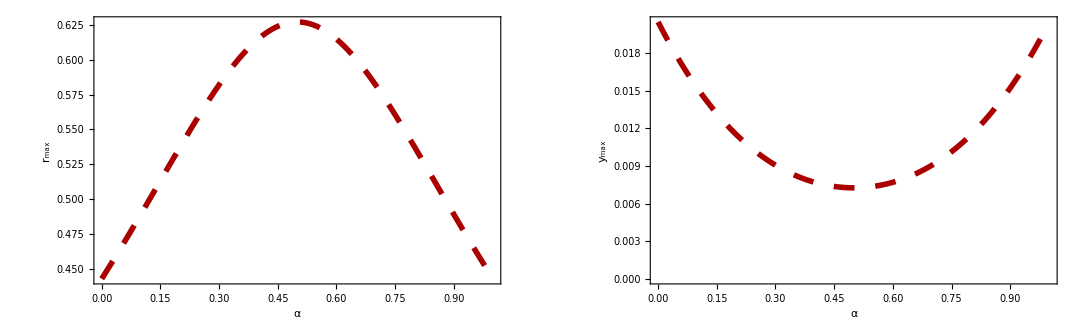

```mathematica
GraphicsGrid[{{
ListPlot[
Table[{α,findmax[α,0.0023,1]_⟦1⟧},{α,0,1,0.01}],
PlotStyle->MyStyle_⟦2⟧,
Joined->True,
Frame->True,
FrameLabel->{"α","r_max"},
LabelStyle->Directive[18,Black],
ImageSize->500
]
,
ListPlot[
Table[{α,findmax[α,0.0023,1]_⟦2⟧},{α,0,1,0.01}],
PlotStyle->MyStyle_⟦2⟧,
Joined->True,
Frame->True,
FrameLabel->{"α","y_max"},
LabelStyle->Directive[18,Black],
ImageSize->500
]
}}]
```

The peak is highest for α=0 or α=1, and it does seem to move around as a function of α.

For given values of (m, Q_s), the absolute maximum occurs at α=0, so we’ll use this value to get the peak height at its highest point.



How does the maximum depend on Q_s ?

Since the peak moves around considerably with Q_s we need to do a little better with the root finder:

```mathematica
findmax3[α_,m_,Q_]:=Module[{temp1},
temp1=FindMaximum[{corr[r,α,m,Q],0<r<rmax},{r,0.2}];
Return[{r/. temp1_⟦2⟧,temp1_⟦1⟧}]
]
```

```mathematica
Upos=Table[{Qs,findmax3[0,0.0023,Qs]_⟦1⟧},{Qs,0.01,3,0.1}];
Dpos=Table[{Qs,findmax3[0,0.0048,Qs]_⟦1⟧},{Qs,0.01,3,0.1}];
Spos=Table[{Qs,findmax3[0,0.095,Qs]_⟦1⟧},{Qs,0.01,3,0.1}];
Cpos=Table[{Qs,findmax3[0,1.29,Qs]_⟦1⟧},{Qs,0.01,3,0.1}];

Uval=Table[{Qs,findmax3[0,0.0023,Qs]_⟦2⟧},{Qs,0.01,3,0.1}];
Dval=Table[{Qs,findmax3[0,0.0048,Qs]_⟦2⟧},{Qs,0.01,3,0.1}];
Sval=Table[{Qs,findmax3[0,0.095,Qs]_⟦2⟧},{Qs,0.01,3,0.1}];
Cval=Table[{Qs,findmax3[0,1.29,Qs]_⟦2⟧},{Qs,0.01,3,0.1}];

PosPlot=ListPlot[
{Upos,Dpos,Spos,Cpos},
PlotStyle->MyStyle,
Joined->True,
Frame->True,
FrameLabel->{"Qs","r_max"},
LabelStyle->Directive[18,Black],
ImageSize->500
];

ValPlot=ListPlot[
{Uval,Dval,Sval,Cval},
PlotStyle->MyStyle,
Joined->True,
Frame->True,
FrameLabel->{"Qs","y_max"},
LabelStyle->Directive[18,Black],
ImageSize->500
];

GraphicsGrid[{{
Show[PosPlot,leg4[{"u","d","s","c"},{0,0.1,0.15}+0.65,{0.85,0.75,0.65,0.55},MyStyle]]
,
Show[ValPlot,leg4[{"u","d","s","c"},{0,0.1,0.15}+0.10,{0.85,0.75,0.65,0.55},MyStyle]]
}}]
```

-Graphics-

With increasing Q_s the peak moves backward (to smaller values of r) and the height of the peak grows almost linearly with Qs

For small Q_s the peak moves outward (to larger r) and the height of the peak shrinks linearly with Qs.

When position of the maximum is larger than the nonperturbative cutoff (default: 0.5 fm) the maximum is just given by the value at the cutoff.


Next let’s use the ceiling at α=0 and test that, for random parameters (m, Qs), the ceiling is always above the curve:

```mathematica
TestMC[]:=Module[{mymass,myQsat,mymax},
mymass=RandomChoice[{0.0023,0.0048,0.095,1.29}];
Print["m = ",mymass];
myQsat=RandomReal[{0.01,3}];
Print["Qs = ",myQsat];
mymax=1.01*FindMaximum[{corr[r,0,mymass,myQsat],0<r<rmax},{r,0.2}]_⟦1⟧;
Print["Ceiling = ",mymax];
Plot3D[{corr[r,α,mymass,myQsat],mymax},{r,0,rmax*1.01},{α,0,1},ImageSize->500]
(*Check[Print[Plot3D[{corr[r,α,mymass,myQsat],mymax},{r,0,3},{α,0,1},ImageSize->500]],
Print["Failure"];
Return[1];
];
Return[0];*)
]
```

```mathematica
TestMC[]
```

m = 0.095

Qs = 2

Ceiling = 0.0426689

-Graphics3D-

Yes, it seems to always correctly find a ceiling for any quark flavor and for a huge range of Qs.    


Now let’s integrate it into the sampler and verify that it reproduces the input distribution.

```mathematica
QuarkSample2[m_,Qs_]:=
Module[{r,α,rfinal="",MCceiling,y},
While[rfinal=="",
r = RandomReal[{0,rmax}];
α=RandomReal[{αmin,1-αmin}];
MCceiling=1.01*FindMaximum[{corr[r,0,m,Qs],0<r<rmax},{r,0.2}]_⟦1⟧;
y = RandomReal[{0,MCceiling}];
If[y<corr[r,α,m,Qs],rfinal=r];
];
Return[{α,rfinal}]
]
```

This routine is just the part which samples the 2D probability distribution.  We’ll test to see if it reproduces the input distribution.

```mathematica
dataset={};
```

```mathematica
thismass=0.095;
thisQ=2;
```

```mathematica
quarkhisto[dα_,dr_]:=Module[{c,pl1,pl2,rawdata,scaleddata,bincenters,histo},
rawdata=BinCounts[dataset,{0,1,dα},{0,rmax,dr}];
scaleddata=rawdata/Max[rawdata];
bincenters = Table[{αmin+(i-1/2)*dα,0+(j-1/2)*dr},{i,1,1/dα},{j,1,rmax/dr}];
histo=Flatten[Table[{bincenters_⟦i,j,1⟧,bincenters_⟦i,j,2⟧,scaleddata_⟦i,j⟧},{i,1,1/dα},{j,1,rmax/dr}],1];
pl1=ListPlot3D[histo,AxesLabel->{"α","r","P(α,r)"},ImageSize->500,LabelStyle->Directive[18,Black],PlotRange->{{0,1},{0,rmax},{0,1}},PlotLabel->"Strange Quarks, Qs = 2 GeV"];

c=FindMaximum[{corr[r,0,thismass,thisQ],0<r<rmax},{r,0.2}]_⟦1⟧;

pl2=Plot3D[corr[r,α,thismass,thisQ]/c,{α,0,1},{r,0,rmax*1.01},AxesLabel->{"α","r","P(α,r)"},ImageSize->500,LabelStyle->Directive[18,Black],PlotStyle->Directive[Green,Opacity[0.5]],PlotRange->{{0,1},{0,rmax},{0,1}}];
Print["N = ",Length[dataset]];
Print["m = ",thismass];
Print["Qs = ",thisQ];
Show[pl1,pl2]
]
```

```mathematica
num=10000;

PrintTemporary["i = ",Dynamic[i]];
For[i=1,i≤num,i++,
AppendTo[dataset,QuarkSample2[thismass,thisQ]]
]

fig=quarkhisto[0.1,0.1]

SetDirectory["C:\\Users\\sieve\\Dropbox\\ICCING"]
Export["Convergence_Test_S_2GeV.pdf",fig]
```

N = 20000

m = 0.095

Qs = 2

-Graphics3D-

C:\Users\sieve\Dropbox\ICCING

Convergence_Test_S_2GeV.pdf

-Graphics-

Success!  The input distribution is successfully reproduced by the MC sampling.

This works for multiple choices of parameters (m, Qs), and it correctly captures the case when the peak is out beyond the cutoff rmax.



Then the corrected version of the splitting routine has two changes:

	Random alpha sample is moved inside the MC “while” loop
	
	New MC ceiling obtained by finding the maximum at α=0.

```mathematica
(* Define the procedure to sample the redistribution of a possible gluon splitting *)
SplittingSample2[Qs_] := Module[{MCceiling,charges,m,IsQuark,o={},r,y,αtemp,rfinal="",ϕ=RandomReal[{0,2π}]},
charges=RollFlavor[Qs];
m=charges_⟦2⟧;
IsQuark=If[charges_⟦1⟧≠"g",True,False];
If[IsQuark,
While[rfinal=="",
r = RandomReal[{0,rmax}];
αtemp=RandomReal[{αmin,1-αmin}];
MCceiling=1.01*FindMaximum[{corr[r,0,m,Qs],0<r<rmax},{r,0.2}]_⟦1⟧;
y = RandomReal[{0,MCceiling}];
If[y<corr[r,αtemp,m,Qs],rfinal=r];
],
Return[{charges,{1,0,0}}];
];
Return[{charges,{αtemp,rfinal Cos[ϕ],rfinal Sin[ϕ]}}]
(* Returns the charges of the selected flavor, the fraction of energy being redistributed, and the displacement:  { {f,m,b,s,q} , {α,Δx,Δy} } *)
]
```